# SQUIRREL & CEREAL CODE CALCULATIONS

January 2022

This notebook is supplementary material for the paper
Relativistic location algorithm in curved spacetime
by Justin C. Feng, Filip Hejda, and Sante Carloni
arXiv:2201.01774

## SRL (CEREAL) CALCULATIONS

### CLEAR VARIABLES

```mathematica
Clear[db,X,ds,h,Xs]
Clear[X1,X2,X3,X4,e1,e2,e3,E1,E2,E3]
Clear[n0,eps4,nx,assum]
Clear[V1,V2,V3,A,B]
Clear[k1,k2,k3,k4,a,c,cc,xo,Dx,Dy,Dz]
```

### MINKOWSKI METRIC

#### DIMENSION AND COORDINATES

##### SPACETIME

Dimension and coordinates

```mathematica
(* DIMENSION *)
db=4;

(* COORDINATES *)
X={t,x,y,z};
```

##### SPATIAL

Constructing the spatial dimension:

```mathematica
(* DIMENSION *)
ds=db-1;
```

#### MINKOWSKI METRIC

##### SPACETIME METRIC

Constructing the Minkowski metric and coordinates:

```mathematica
(* MINKOWSKI METRIC *)
η=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

##### SPATIAL METRIC

Constructing the spatial metric and coordinates:

```mathematica
(* SPATIAL METRIC *)
h=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

### FRAME

This section of the notebook constructs a frame from four spacelike separated points in Minkowski space.

#### INPUT POINTS

Here are the coordinates for the input points:

```mathematica
X1={t1,x1,y1,z1};
X2={t2,x2,y2,z2};
X3={t3,x3,y3,z3};
X4={t4,x4,y4,z4};

assum={X1∈Reals,X2∈Reals,X3∈Reals,X4∈Reals};
```

#### SPATIAL BASIS

Here, a basis for a spacelike slice is constructed:

e_1^μ=X_2^μ-X_1^μ

e_2^μ=X_3^μ-X_1^μ

e_3^μ=X_4^μ-X_1^μ

```mathematica
e1=X2-X1;
e2=X3-X1;
e3=X4-X1;
```

```mathematica
E1={E11,E21,E31,E41};
E2={E12,E22,E32,E42};
E3={E13,E23,E33,E43};

assum=Join[assum,{E1∈Reals,E2∈Reals,E3∈Reals}];
```

#### NORMAL VECTOR

##### CONSTRUCTION

The normal vector is:

n_0^μ=η^μσ ϵ_σαβγ e_1^α e_2^β e_3^γ

```mathematica
eps4=LeviCivitaTensor[4];
```

```mathematica
n0=Table[Sum[η[[mi,ii]]eps4[[ii,ji,ki,li]]E1[[ji]]E2[[ki]]E3[[li]],{ii,1,db},{ji,1,db},{ki,1,db},{li,1,db}],{mi,1,db}];
```

```mathematica
n0[[1]]
```

E23 E32 E41-E22 E33 E41-E23 E31 E42+E21 E33 E42+E22 E31 E43-E21 E32 E43

##### FORTRAN FORM

```mathematica
FortranForm[n0[[1]]]
```

E23*E32*E41 - E22*E33*E41 - E23*E31*E42 + E21*E33*E42 + E22*E31*E43 - E21*E32*E43

```mathematica
FortranForm[n0[[2]]]
```

E13*E32*E41 - E12*E33*E41 - E13*E31*E42 + E11*E33*E42 + E12*E31*E43 - E11*E32*E43

```mathematica
FortranForm[n0[[3]]]
```

-(E13*E22*E41) + E12*E23*E41 + E13*E21*E42 - E11*E23*E42 - E12*E21*E43 + E11*E22*E43

```mathematica
FortranForm[n0[[4]]]
```

E13*E22*E31 - E12*E23*E31 - E13*E21*E32 + E11*E23*E32 + E12*E21*E33 - E11*E22*E33

##### UNIT NORMAL VECTOR

From this, one may construct a unit normal vector:

n^μ=n_0^μ/(√(-η_στ n_0^σ n_0^τ))

```mathematica
Simplify[-Sum[η[[ii,ji]]n0[[ii]]n0[[ji]],{ii,1,db},{ji,1,db}],Assumptions->assum];
nx=q*n0/(√%);
```

##### CHECKING ORTHOGONALITY

```mathematica
E1.η.n0//Simplify
E2.η.n0//Simplify
E3.η.n0//Simplify
```

0

0

0

```mathematica
E1.η.nx//Simplify
E2.η.nx//Simplify
E3.η.nx//Simplify
```

0

0

0

### TETRAHEDRAL CIRCUMCENTER CALCULATIONS

#### Levy-Liu Version

```mathematica
X1={x1,y1,z1};
X2={x2,y2,z2};
X3={x3,y3,z3};
X4={x4,y4,z4};

V1=X2-X1;
V2=X3-X1;
V3=X4-X1;

B={X2.X2-X1.X1,X3.X3-X1.X1,X4.X4-X1.X1}/2;
```

```mathematica
A={V1,V2,V3}//FullSimplify;
```

```mathematica
MatrixForm[A]
```

(-x1+x2 | -y1+y2 | -z1+z2
-x1+x3 | -y1+y3 | -z1+z3
-x1+x4 | -y1+y4 | -z1+z4)

```mathematica
A[[1,1]]
```

-x1+x2

```mathematica
cc=Inverse[A].B//FullSimplify
```

{((y3 (-z1+z2)+y2 (z1-z3)+y1 (-z2+z3)) (x1^2-x4^2+y1^2-y4^2+z1^2-z4^2)+(x1^2-x3^2+y1^2-y3^2+z1^2-z3^2) (y4 (z1-z2)+y1 (z2-z4)+y2 (-z1+z4))+(-x1^2+x2^2-y1^2+y2^2-z1^2+z2^2) (y4 (z1-z3)+y1 (z3-z4)+y3 (-z1+z4)))/(2 (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4))),((x3 (z1-z2)+x1 (z2-z3)+x2 (-z1+z3)) (x1^2-x4^2+y1^2-y4^2+z1^2-z4^2)+(-x1^2+x3^2-y1^2+y3^2-z1^2+z3^2) (x4 (z1-z2)+x1 (z2-z4)+x2 (-z1+z4))+(x1^2-x2^2+y1^2-y2^2+z1^2-z2^2) (x4 (z1-z3)+x1 (z3-z4)+x3 (-z1+z4)))/(2 (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4))),((x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)) (x1^2-x2^2+y1^2-y2^2+z1^2-z2^2)+(x4 (y1-y2)+x1 (y2-y4)+x2 (-y1+y4)) (x1^2-x3^2+y1^2-y3^2+z1^2-z3^2)+(x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3)) (x1^2-x4^2+y1^2-y4^2+z1^2-z4^2))/(2 (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4)))}

#### Mathworld Version

```mathematica
k1=x1^2+y1^2+z1^2;
k2=x2^2+y2^2+z2^2;
k3=x3^2+y3^2+z3^2;
k4=x4^2+y4^2+z4^2;
```

```mathematica
a=Det[({{x1, y1, z1, 1}, {x2, y2, z2, 1}, {x3, y3, z3, 1}, {x4, y4, z4, 1}})];

c=Det[({{k1, x1, y1, z1}, {k2, x2, y2, z2}, {k3, x3, y3, z3}, {k4, x4, y4, z4}})];
Dx=Det[({{k1, y1, z1, 1}, {k2, y2, z2, 1}, {k3, y3, z3, 1}, {k4, y4, z4, 1}})];
Dy=-Det[({{k1, x1, z1, 1}, {k2, x2, z2, 1}, {k3, x3, z3, 1}, {k4, x4, z4, 1}})];
Dz=Det[({{k1, x1, y1, 1}, {k2, x2, y2, 1}, {k3, x3, y3, 1}, {k4, x4, y4, 1}})];
```

```mathematica
xo=Simplify[Dx/(2 a)];
yo=Simplify[Dy/(2 a)];
zo=Simplify[Dz/(2 a)];
```

```mathematica
((x2-xo)^2+(y2-yo)^2+(z2-zo)^2)-((x1-xo)^2+(y1-yo)^2+(z1-zo)^2)//Simplify
```

0

```mathematica
((x3-xo)^2+(y3-yo)^2+(z3-zo)^2)-((x1-xo)^2+(y1-yo)^2+(z1-zo)^2)//Simplify
```

0

```mathematica
((x4-xo)^2+(y4-yo)^2+(z4-zo)^2)-((x1-xo)^2+(y1-yo)^2+(z1-zo)^2)//Simplify
```

0

```mathematica
cc[[1]]-xo//Simplify
cc[[2]]-yo//Simplify
cc[[3]]-zo//Simplify
```

0

0

0

#### Brute Force Version

##### Raw Solutions

```mathematica
Solve[{(x1-xc)^2+(y1-yc)^2+(z1-zc)^2==(x2-xc)^2+(y2-yc)^2+(z2-zc)^2,(x2-xc)^2+(y2-yc)^2+(z2-zc)^2==(x3-xc)^2+(y3-yc)^2+(z3-zc)^2,(x3-xc)^2+(y3-yc)^2+(z3-zc)^2==(x4-xc)^2+(y4-yc)^2+(z4-zc)^2},{xc,yc,zc}][[1]]//FullSimplify;
solsbf=%;
```

```mathematica
xc/.solsbf
```

-(-4 (2 (x1^2-x2^2+y1^2-y2^2+z1^2-z2^2) (z2-z3)-2 (z1-z2) (x2^2-x3^2+y2^2-y3^2+z2^2-z3^2)) ((y3-y4) (z1-z2)-(y1-y2) (z3-z4))+4 (y3 (-z1+z2)+y2 (z1-z3)+y1 (-z2+z3)) (2 (z1-z2) (-x3^2+x4^2-y3^2+y4^2+(z1+z2-z3-z4) (z3-z4))+2 (x1^2-x2^2+y1^2-y2^2) (z3-z4)))/(16 (z1-z2) (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4)))

```mathematica
yc/.solsbf
```

(-x4 y2^2 z1+x4 y3^2 z1+x1^2 x4 z2-x1 x4^2 z2+x4 y1^2 z2+x1 y3^2 z2-x4 y3^2 z2-x1 y4^2 z2+x4 z1^2 z2-x4 z1 z2^2-x1^2 x4 z3+x1 x4^2 z3-x4 y1^2 z3-x1 y2^2 z3+x4 y2^2 z3+x1 y4^2 z3-x4 z1^2 z3-x1 z2^2 z3+x4 z2^2 z3+x4 z1 z3^2+x1 z2 z3^2-x4 z2 z3^2+x3^2 (x4 (z1-z2)+x1 (z2-z4))+x1 (y2^2-y3^2+z2^2-z3^2) z4+x1 (-z2+z3) z4^2+x2 (-y3^2 z1+y4^2 z1+x4^2 (z1-z3)-y4^2 z3+z1^2 z3-z1 z3^2+(x1^2+y1^2) (z3-z4)+(y3^2-z1^2+z3^2) z4+(z1-z3) z4^2+x3^2 (-z1+z4))+x2^2 (x4 (-z1+z3)+x3 (z1-z4)+x1 (-z3+z4))+x3 (x4^2 (-z1+z2)+y2^2 (z1-z4)-(x1^2+y1^2) (z2-z4)-(z1-z2) (y4^2+z1 z2-(z1+z2) z4+z4^2)))/(2 (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4)))

```mathematica
zc/.solsbf
```

(-x1^2 x4 y2+x1 x4^2 y2-x4 y1^2 y2+x4 y1 y2^2+x1^2 x4 y3-x1 x4^2 y3+x4 y1^2 y3+x1 y2^2 y3-x4 y2^2 y3-x4 y1 y3^2-x1 y2 y3^2+x4 y2 y3^2-x1 y2^2 y4+x1 y3^2 y4+x1 y2 y4^2-x1 y3 y4^2+x2^2 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x3^2 (x4 (-y1+y2)+x1 (-y2+y4))-x4 y2 z1^2+x4 y3 z1^2+x4 y1 z2^2+x1 y3 z2^2-x4 y3 z2^2-x1 y4 z2^2-x4 y1 z3^2-x1 y2 z3^2+x4 y2 z3^2+x1 y4 z3^2+x1 (y2-y3) z4^2+x2 (-x1^2 y3-y1^2 y3+y1 y3^2+x4^2 (-y1+y3)+x3^2 (y1-y4)+x1^2 y4+y1^2 y4-y3^2 y4-y1 y4^2+y3 y4^2-y3 z1^2+y4 z1^2+y1 z3^2-y4 z3^2+(-y1+y3) z4^2)+x3 (x4^2 (y1-y2)+x1^2 (y2-y4)+y1^2 (y2-y4)+y2^2 y4-y2 y4^2+y2 z1^2-y4 z1^2+y4 z2^2-y2 z4^2+y1 (-y2^2+y4^2-z2^2+z4^2)))/(2 (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4)))

##### Simplified solutions and input form

```mathematica
dens= (-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)+(-x2 y1+x1 y2-x1 y3+x2 y3) z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4));
```

```mathematica
dens//Expand//InputForm
```

x3*y2*z1 - x4*y2*z1 - x2*y3*z1 + x4*y3*z1 + x2*y4*z1 - x3*y4*z1 - x3*y1*z2 + x4*y1*z2 + x1*y3*z2 - x4*y3*z2 - x1*y4*z2 + x3*y4*z2 + x2*y1*z3 - x4*y1*z3 - x1*y2*z3 + x4*y2*z3 + x1*y4*z3 - x2*y4*z3 - x2*y1*z4 + x3*y1*z4 + x1*y2*z4 - x3*y2*z4 - 
 x1*y3*z4 + x2*y3*z4

```mathematica
2(z1-z2) dens*xc/.solsbf//Simplify//Expand//InputForm
```

x3^2*y2*z1^2 - x4^2*y2*z1^2 - x2^2*y3*z1^2 + x4^2*y3*z1^2 - y2^2*y3*z1^2 + y2*y3^2*z1^2 + x2^2*y4*z1^2 - x3^2*y4*z1^2 + y2^2*y4*z1^2 - y3^2*y4*z1^2 - y2*y4^2*z1^2 + y3*y4^2*z1^2 - x3^2*y1*z1*z2 + x4^2*y1*z1*z2 - x3^2*y2*z1*z2 + x4^2*y2*z1*z2 + 
 x1^2*y3*z1*z2 + x2^2*y3*z1*z2 - 2*x4^2*y3*z1*z2 + y1^2*y3*z1*z2 + y2^2*y3*z1*z2 - y1*y3^2*z1*z2 - y2*y3^2*z1*z2 - x1^2*y4*z1*z2 - x2^2*y4*z1*z2 + 2*x3^2*y4*z1*z2 - y1^2*y4*z1*z2 - y2^2*y4*z1*z2 + 2*y3^2*y4*z1*z2 + y1*y4^2*z1*z2 + y2*y4^2*z1*z2 - 
 2*y3*y4^2*z1*z2 + y3*z1^3*z2 - y4*z1^3*z2 + x3^2*y1*z2^2 - x4^2*y1*z2^2 - x1^2*y3*z2^2 + x4^2*y3*z2^2 - y1^2*y3*z2^2 + y1*y3^2*z2^2 + x1^2*y4*z2^2 - x3^2*y4*z2^2 + y1^2*y4*z2^2 - y3^2*y4*z2^2 - y1*y4^2*z2^2 + y3*y4^2*z2^2 - 2*y3*z1^2*z2^2 + 
 2*y4*z1^2*z2^2 + y3*z1*z2^3 - y4*z1*z2^3 + x2^2*y1*z1*z3 - x4^2*y1*z1*z3 - x1^2*y2*z1*z3 + x4^2*y2*z1*z3 - y1^2*y2*z1*z3 + y1*y2^2*z1*z3 + x1^2*y4*z1*z3 - x2^2*y4*z1*z3 + y1^2*y4*z1*z3 - y2^2*y4*z1*z3 - y1*y4^2*z1*z3 + y2*y4^2*z1*z3 - 
 y2*z1^3*z3 + y4*z1^3*z3 - x2^2*y1*z2*z3 + x4^2*y1*z2*z3 + x1^2*y2*z2*z3 - x4^2*y2*z2*z3 + y1^2*y2*z2*z3 - y1*y2^2*z2*z3 - x1^2*y4*z2*z3 + x2^2*y4*z2*z3 - y1^2*y4*z2*z3 + y2^2*y4*z2*z3 + y1*y4^2*z2*z3 - y2*y4^2*z2*z3 + y2*z1^2*z2*z3 - 
 y4*z1^2*z2*z3 + y1*z1*z2^2*z3 - y4*z1*z2^2*z3 - y1*z2^3*z3 + y4*z2^3*z3 + y2*z1^2*z3^2 - y4*z1^2*z3^2 - y1*z1*z2*z3^2 - y2*z1*z2*z3^2 + 2*y4*z1*z2*z3^2 + y1*z2^2*z3^2 - y4*z2^2*z3^2 - x2^2*y1*z1*z4 + x3^2*y1*z1*z4 + x1^2*y2*z1*z4 - 
 x3^2*y2*z1*z4 + y1^2*y2*z1*z4 - y1*y2^2*z1*z4 - x1^2*y3*z1*z4 + x2^2*y3*z1*z4 - y1^2*y3*z1*z4 + y2^2*y3*z1*z4 + y1*y3^2*z1*z4 - y2*y3^2*z1*z4 + y2*z1^3*z4 - y3*z1^3*z4 + x2^2*y1*z2*z4 - x3^2*y1*z2*z4 - x1^2*y2*z2*z4 + x3^2*y2*z2*z4 - 
 y1^2*y2*z2*z4 + y1*y2^2*z2*z4 + x1^2*y3*z2*z4 - x2^2*y3*z2*z4 + y1^2*y3*z2*z4 - y2^2*y3*z2*z4 - y1*y3^2*z2*z4 + y2*y3^2*z2*z4 - y2*z1^2*z2*z4 + y3*z1^2*z2*z4 - y1*z1*z2^2*z4 + y3*z1*z2^2*z4 + y1*z2^3*z4 - y3*z2^3*z4 + y1*z1*z3^2*z4 - 
 y2*z1*z3^2*z4 - y1*z2*z3^2*z4 + y2*z2*z3^2*z4 - y2*z1^2*z4^2 + y3*z1^2*z4^2 + y1*z1*z2*z4^2 + y2*z1*z2*z4^2 - 2*y3*z1*z2*z4^2 - y1*z2^2*z4^2 + y3*z2^2*z4^2 - y1*z1*z3*z4^2 + y2*z1*z3*z4^2 + y1*z2*z3*z4^2 - y2*z2*z3*z4^2

```mathematica
2dens*yc/.solsbf//Simplify//Expand//InputForm
```

x2^2*x3*z1 - x2*x3^2*z1 - x2^2*x4*z1 + x3^2*x4*z1 + x2*x4^2*z1 - x3*x4^2*z1 + x3*y2^2*z1 - x4*y2^2*z1 - x2*y3^2*z1 + x4*y3^2*z1 + x2*y4^2*z1 - x3*y4^2*z1 - x1^2*x3*z2 + x1*x3^2*z2 + x1^2*x4*z2 - x3^2*x4*z2 - x1*x4^2*z2 + x3*x4^2*z2 - x3*y1^2*z2 + 
 x4*y1^2*z2 + x1*y3^2*z2 - x4*y3^2*z2 - x1*y4^2*z2 + x3*y4^2*z2 - x3*z1^2*z2 + x4*z1^2*z2 + x3*z1*z2^2 - x4*z1*z2^2 + x1^2*x2*z3 - x1*x2^2*z3 - x1^2*x4*z3 + x2^2*x4*z3 + x1*x4^2*z3 - x2*x4^2*z3 + x2*y1^2*z3 - x4*y1^2*z3 - x1*y2^2*z3 + x4*y2^2*z3 + 
 x1*y4^2*z3 - x2*y4^2*z3 + x2*z1^2*z3 - x4*z1^2*z3 - x1*z2^2*z3 + x4*z2^2*z3 - x2*z1*z3^2 + x4*z1*z3^2 + x1*z2*z3^2 - x4*z2*z3^2 - x1^2*x2*z4 + x1*x2^2*z4 + x1^2*x3*z4 - x2^2*x3*z4 - x1*x3^2*z4 + x2*x3^2*z4 - x2*y1^2*z4 + x3*y1^2*z4 + x1*y2^2*z4 - 
 x3*y2^2*z4 - x1*y3^2*z4 + x2*y3^2*z4 - x2*z1^2*z4 + x3*z1^2*z4 + x1*z2^2*z4 - x3*z2^2*z4 - x1*z3^2*z4 + x2*z3^2*z4 + x2*z1*z4^2 - x3*z1*z4^2 - x1*z2*z4^2 + x3*z2*z4^2 + x1*z3*z4^2 - x2*z3*z4^2

```mathematica
2dens*zc/.solsbf//Simplify//Expand//InputForm
```

-(x2^2*x3*y1) + x2*x3^2*y1 + x2^2*x4*y1 - x3^2*x4*y1 - x2*x4^2*y1 + x3*x4^2*y1 + x1^2*x3*y2 - x1*x3^2*y2 - x1^2*x4*y2 + x3^2*x4*y2 + x1*x4^2*y2 - x3*x4^2*y2 + x3*y1^2*y2 - x4*y1^2*y2 - x3*y1*y2^2 + x4*y1*y2^2 - x1^2*x2*y3 + x1*x2^2*y3 + 
 x1^2*x4*y3 - x2^2*x4*y3 - x1*x4^2*y3 + x2*x4^2*y3 - x2*y1^2*y3 + x4*y1^2*y3 + x1*y2^2*y3 - x4*y2^2*y3 + x2*y1*y3^2 - x4*y1*y3^2 - x1*y2*y3^2 + x4*y2*y3^2 + x1^2*x2*y4 - x1*x2^2*y4 - x1^2*x3*y4 + x2^2*x3*y4 + x1*x3^2*y4 - x2*x3^2*y4 + x2*y1^2*y4 - 
 x3*y1^2*y4 - x1*y2^2*y4 + x3*y2^2*y4 + x1*y3^2*y4 - x2*y3^2*y4 - x2*y1*y4^2 + x3*y1*y4^2 + x1*y2*y4^2 - x3*y2*y4^2 - x1*y3*y4^2 + x2*y3*y4^2 + x3*y2*z1^2 - x4*y2*z1^2 - x2*y3*z1^2 + x4*y3*z1^2 + x2*y4*z1^2 - x3*y4*z1^2 - x3*y1*z2^2 + x4*y1*z2^2 + 
 x1*y3*z2^2 - x4*y3*z2^2 - x1*y4*z2^2 + x3*y4*z2^2 + x2*y1*z3^2 - x4*y1*z3^2 - x1*y2*z3^2 + x4*y2*z3^2 + x1*y4*z3^2 - x2*y4*z3^2 - x2*y1*z4^2 + x3*y1*z4^2 + x1*y2*z4^2 - x3*y2*z4^2 - x1*y3*z4^2 + x2*y3*z4^2

### TIMELIKE HYPERPLANE LOCATOR BRUTE FORCE

#### T-ORIENTED

##### Raw solutions

```mathematica
Solve[{(x1-xc)^2+(y1-yc)^2-(t1-tc)^2==(x2-xc)^2+(y2-yc)^2-(t2-tc)^2,(x2-xc)^2+(y2-yc)^2-(t2-tc)^2==(x3-xc)^2+(y3-yc)^2-(t3-tc)^2,(x3-xc)^2+(y3-yc)^2-(t3-tc)^2==(x4-xc)^2+(y4-yc)^2-(t4-tc)^2},{tc,xc,yc}][[1]]//FullSimplify;
soltbf=%;
```

```mathematica
tc/.soltbf
```

(-4 (-2 (t1^2-t2^2-x1^2+x2^2-y1^2+y2^2) (y2-y3)+2 (y1-y2) (t2^2-t3^2-x2^2+x3^2-y2^2+y3^2)) ((x3-x4) (y1-y2)-(x1-x2) (y3-y4))+4 (x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3)) (-2 (t1^2-t2^2-x1^2+x2^2-y1^2+y2^2) (y3-y4)+2 (y1-y2) (t3^2-t4^2-x3^2+x4^2-y3^2+y4^2)))/(16 (y1-y2) (-t2 x3 y1+t2 x4 y1+t1 x3 y2-t1 x4 y2+t2 x1 y3-t1 x2 y3+t1 x4 y3-t2 x4 y3+t4 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-t2 x1+t1 x2-t1 x3+t2 x3) y4+t3 (-x4 y1-x1 y2+x4 y2+x2 (y1-y4)+x1 y4)))

```mathematica
xc/.soltbf
```

(-t4 x2^2 y1+t4 x3^2 y1-t1^2 t4 y2+t1 t4^2 y2+t4 x1^2 y2+t1 x3^2 y2-t4 x3^2 y2-t1 x4^2 y2+t4 y1^2 y2-t4 y1 y2^2+t1^2 t4 y3-t1 t4^2 y3-t4 x1^2 y3-t1 x2^2 y3+t4 x2^2 y3+t1 x4^2 y3-t4 y1^2 y3-t1 y2^2 y3+t4 y2^2 y3+t4 y1 y3^2+t1 y2 y3^2-t4 y2 y3^2+t1 (x2^2-x3^2+y2^2-y3^2) y4+t1 (-y2+y3) y4^2+t2 (-x3^2 y1+x4^2 y1-x4^2 y3+y1^2 y3-y1 y3^2+t4^2 (-y1+y3)+t3^2 (y1-y4)-(t1-x1) (t1+x1) (y3-y4)+(x3^2-y1^2+y3^2) y4+(y1-y3) y4^2)+t2^2 (t4 (y1-y3)+t1 (y3-y4)+t3 (-y1+y4))+t3^2 (t4 (-y1+y2)+t1 (-y2+y4))+t3 (t4^2 (y1-y2)+x2^2 (y1-y4)+(t1-x1) (t1+x1) (y2-y4)-(y1-y2) (x4^2+y1 y2-(y1+y2) y4+y4^2)))/(2 (-t2 x3 y1+t2 x4 y1+t1 x3 y2-t1 x4 y2+t2 x1 y3-t1 x2 y3+t1 x4 y3-t2 x4 y3+t4 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-t2 x1+t1 x2-t1 x3+t2 x3) y4+t3 (-x4 y1-x1 y2+x4 y2+x2 (y1-y4)+x1 y4)))

```mathematica
yc/.soltbf
```

(t1^2 t4 x2-t1 t4^2 x2-t4 x1^2 x2+t4 x1 x2^2-t1^2 t4 x3+t1 t4^2 x3+t4 x1^2 x3+t1 x2^2 x3-t4 x2^2 x3-t4 x1 x3^2-t1 x2 x3^2+t4 x2 x3^2+t3^2 (t4 (x1-x2)+t1 (x2-x4))-t1 x2^2 x4+t1 x3^2 x4+t1 x2 x4^2-t1 x3 x4^2+t2^2 (t4 (-x1+x3)+t3 (x1-x4)+t1 (-x3+x4))-t4 x2 y1^2+t4 x3 y1^2+t4 x1 y2^2+t1 x3 y2^2-t4 x3 y2^2-t1 x4 y2^2-t4 x1 y3^2-t1 x2 y3^2+t4 x2 y3^2+t1 x4 y3^2+t1 (x2-x3) y4^2+t2 (t4^2 (x1-x3)+t1^2 x3-x1^2 x3+x1 x3^2-t1^2 x4+x1^2 x4-x3^2 x4-x1 x4^2+x3 x4^2+t3^2 (-x1+x4)-x3 y1^2+x4 y1^2+x1 y3^2-x4 y3^2+(-x1+x3) y4^2)+t3 (t4^2 (-x1+x2)+x1^2 (x2-x4)+x2^2 x4-x2 x4^2+t1^2 (-x2+x4)+x2 y1^2-x4 y1^2+x4 y2^2-x2 y4^2+x1 (-x2^2+x4^2-y2^2+y4^2)))/(2 (-t2 x3 y1+t2 x4 y1+t1 x3 y2-t1 x4 y2+t2 x1 y3-t1 x2 y3+t1 x4 y3-t2 x4 y3+t4 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-t2 x1+t1 x2-t1 x3+t2 x3) y4+t3 (-x4 y1-x1 y2+x4 y2+x2 (y1-y4)+x1 y4)))

##### Simplified solutions & input form

```mathematica
den=(-t2 x3 y1+t2 x4 y1+t1 x3 y2-t1 x4 y2+t2 x1 y3-t1 x2 y3+t1 x4 y3-t2 x4 y3+t4 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-t2 x1+t1 x2-t1 x3+t2 x3) y4+t3 (-x4 y1-x1 y2+x4 y2+x2 (y1-y4)+x1 y4));
den//Expand//InputForm
```

t3*x2*y1 - t4*x2*y1 - t2*x3*y1 + t4*x3*y1 + t2*x4*y1 - t3*x4*y1 - t3*x1*y2 + t4*x1*y2 + t1*x3*y2 - t4*x3*y2 - t1*x4*y2 + t3*x4*y2 + t2*x1*y3 - t4*x1*y3 - t1*x2*y3 + t4*x2*y3 + t1*x4*y3 - t2*x4*y3 - t2*x1*y4 + t3*x1*y4 + t1*x2*y4 - t3*x2*y4 - 
 t1*x3*y4 + t2*x3*y4

```mathematica
2(y1-y2)*den*tc/.soltbf//Expand//InputForm
```

t3^2*x2*y1^2 - t4^2*x2*y1^2 - t2^2*x3*y1^2 + t4^2*x3*y1^2 + x2^2*x3*y1^2 - x2*x3^2*y1^2 + t2^2*x4*y1^2 - t3^2*x4*y1^2 - x2^2*x4*y1^2 + x3^2*x4*y1^2 + x2*x4^2*y1^2 - x3*x4^2*y1^2 - t3^2*x1*y1*y2 + t4^2*x1*y1*y2 - t3^2*x2*y1*y2 + t4^2*x2*y1*y2 + 
 t1^2*x3*y1*y2 + t2^2*x3*y1*y2 - 2*t4^2*x3*y1*y2 - x1^2*x3*y1*y2 - x2^2*x3*y1*y2 + x1*x3^2*y1*y2 + x2*x3^2*y1*y2 - t1^2*x4*y1*y2 - t2^2*x4*y1*y2 + 2*t3^2*x4*y1*y2 + x1^2*x4*y1*y2 + x2^2*x4*y1*y2 - 2*x3^2*x4*y1*y2 - x1*x4^2*y1*y2 - x2*x4^2*y1*y2 + 
 2*x3*x4^2*y1*y2 - x3*y1^3*y2 + x4*y1^3*y2 + t3^2*x1*y2^2 - t4^2*x1*y2^2 - t1^2*x3*y2^2 + t4^2*x3*y2^2 + x1^2*x3*y2^2 - x1*x3^2*y2^2 + t1^2*x4*y2^2 - t3^2*x4*y2^2 - x1^2*x4*y2^2 + x3^2*x4*y2^2 + x1*x4^2*y2^2 - x3*x4^2*y2^2 + 2*x3*y1^2*y2^2 - 
 2*x4*y1^2*y2^2 - x3*y1*y2^3 + x4*y1*y2^3 + t2^2*x1*y1*y3 - t4^2*x1*y1*y3 - t1^2*x2*y1*y3 + t4^2*x2*y1*y3 + x1^2*x2*y1*y3 - x1*x2^2*y1*y3 + t1^2*x4*y1*y3 - t2^2*x4*y1*y3 - x1^2*x4*y1*y3 + x2^2*x4*y1*y3 + x1*x4^2*y1*y3 - x2*x4^2*y1*y3 + 
 x2*y1^3*y3 - x4*y1^3*y3 - t2^2*x1*y2*y3 + t4^2*x1*y2*y3 + t1^2*x2*y2*y3 - t4^2*x2*y2*y3 - x1^2*x2*y2*y3 + x1*x2^2*y2*y3 - t1^2*x4*y2*y3 + t2^2*x4*y2*y3 + x1^2*x4*y2*y3 - x2^2*x4*y2*y3 - x1*x4^2*y2*y3 + x2*x4^2*y2*y3 - x2*y1^2*y2*y3 + 
 x4*y1^2*y2*y3 - x1*y1*y2^2*y3 + x4*y1*y2^2*y3 + x1*y2^3*y3 - x4*y2^3*y3 - x2*y1^2*y3^2 + x4*y1^2*y3^2 + x1*y1*y2*y3^2 + x2*y1*y2*y3^2 - 2*x4*y1*y2*y3^2 - x1*y2^2*y3^2 + x4*y2^2*y3^2 - t2^2*x1*y1*y4 + t3^2*x1*y1*y4 + t1^2*x2*y1*y4 - 
 t3^2*x2*y1*y4 - x1^2*x2*y1*y4 + x1*x2^2*y1*y4 - t1^2*x3*y1*y4 + t2^2*x3*y1*y4 + x1^2*x3*y1*y4 - x2^2*x3*y1*y4 - x1*x3^2*y1*y4 + x2*x3^2*y1*y4 - x2*y1^3*y4 + x3*y1^3*y4 + t2^2*x1*y2*y4 - t3^2*x1*y2*y4 - t1^2*x2*y2*y4 + t3^2*x2*y2*y4 + 
 x1^2*x2*y2*y4 - x1*x2^2*y2*y4 + t1^2*x3*y2*y4 - t2^2*x3*y2*y4 - x1^2*x3*y2*y4 + x2^2*x3*y2*y4 + x1*x3^2*y2*y4 - x2*x3^2*y2*y4 + x2*y1^2*y2*y4 - x3*y1^2*y2*y4 + x1*y1*y2^2*y4 - x3*y1*y2^2*y4 - x1*y2^3*y4 + x3*y2^3*y4 - x1*y1*y3^2*y4 + 
 x2*y1*y3^2*y4 + x1*y2*y3^2*y4 - x2*y2*y3^2*y4 + x2*y1^2*y4^2 - x3*y1^2*y4^2 - x1*y1*y2*y4^2 - x2*y1*y2*y4^2 + 2*x3*y1*y2*y4^2 + x1*y2^2*y4^2 - x3*y2^2*y4^2 + x1*y1*y3*y4^2 - x2*y1*y3*y4^2 - x1*y2*y3*y4^2 + x2*y2*y3*y4^2

```mathematica
2*den*xc/.soltbf//Expand//InputForm
```

-(t2^2*t3*y1) + t2*t3^2*y1 + t2^2*t4*y1 - t3^2*t4*y1 - t2*t4^2*y1 + t3*t4^2*y1 + t3*x2^2*y1 - t4*x2^2*y1 - t2*x3^2*y1 + t4*x3^2*y1 + t2*x4^2*y1 - t3*x4^2*y1 + t1^2*t3*y2 - t1*t3^2*y2 - t1^2*t4*y2 + t3^2*t4*y2 + t1*t4^2*y2 - t3*t4^2*y2 - 
 t3*x1^2*y2 + t4*x1^2*y2 + t1*x3^2*y2 - t4*x3^2*y2 - t1*x4^2*y2 + t3*x4^2*y2 - t3*y1^2*y2 + t4*y1^2*y2 + t3*y1*y2^2 - t4*y1*y2^2 - t1^2*t2*y3 + t1*t2^2*y3 + t1^2*t4*y3 - t2^2*t4*y3 - t1*t4^2*y3 + t2*t4^2*y3 + t2*x1^2*y3 - t4*x1^2*y3 - t1*x2^2*y3 + 
 t4*x2^2*y3 + t1*x4^2*y3 - t2*x4^2*y3 + t2*y1^2*y3 - t4*y1^2*y3 - t1*y2^2*y3 + t4*y2^2*y3 - t2*y1*y3^2 + t4*y1*y3^2 + t1*y2*y3^2 - t4*y2*y3^2 + t1^2*t2*y4 - t1*t2^2*y4 - t1^2*t3*y4 + t2^2*t3*y4 + t1*t3^2*y4 - t2*t3^2*y4 - t2*x1^2*y4 + t3*x1^2*y4 + 
 t1*x2^2*y4 - t3*x2^2*y4 - t1*x3^2*y4 + t2*x3^2*y4 - t2*y1^2*y4 + t3*y1^2*y4 + t1*y2^2*y4 - t3*y2^2*y4 - t1*y3^2*y4 + t2*y3^2*y4 + t2*y1*y4^2 - t3*y1*y4^2 - t1*y2*y4^2 + t3*y2*y4^2 + t1*y3*y4^2 - t2*y3*y4^2

```mathematica
2*den*yc/.soltbf//Expand//InputForm
```

t2^2*t3*x1 - t2*t3^2*x1 - t2^2*t4*x1 + t3^2*t4*x1 + t2*t4^2*x1 - t3*t4^2*x1 - t1^2*t3*x2 + t1*t3^2*x2 + t1^2*t4*x2 - t3^2*t4*x2 - t1*t4^2*x2 + t3*t4^2*x2 + t3*x1^2*x2 - t4*x1^2*x2 - t3*x1*x2^2 + t4*x1*x2^2 + t1^2*t2*x3 - t1*t2^2*x3 - t1^2*t4*x3 + 
 t2^2*t4*x3 + t1*t4^2*x3 - t2*t4^2*x3 - t2*x1^2*x3 + t4*x1^2*x3 + t1*x2^2*x3 - t4*x2^2*x3 + t2*x1*x3^2 - t4*x1*x3^2 - t1*x2*x3^2 + t4*x2*x3^2 - t1^2*t2*x4 + t1*t2^2*x4 + t1^2*t3*x4 - t2^2*t3*x4 - t1*t3^2*x4 + t2*t3^2*x4 + t2*x1^2*x4 - t3*x1^2*x4 - 
 t1*x2^2*x4 + t3*x2^2*x4 + t1*x3^2*x4 - t2*x3^2*x4 - t2*x1*x4^2 + t3*x1*x4^2 + t1*x2*x4^2 - t3*x2*x4^2 - t1*x3*x4^2 + t2*x3*x4^2 + t3*x2*y1^2 - t4*x2*y1^2 - t2*x3*y1^2 + t4*x3*y1^2 + t2*x4*y1^2 - t3*x4*y1^2 - t3*x1*y2^2 + t4*x1*y2^2 + t1*x3*y2^2 - 
 t4*x3*y2^2 - t1*x4*y2^2 + t3*x4*y2^2 + t2*x1*y3^2 - t4*x1*y3^2 - t1*x2*y3^2 + t4*x2*y3^2 + t1*x4*y3^2 - t2*x4*y3^2 - t2*x1*y4^2 + t3*x1*y4^2 + t1*x2*y4^2 - t3*x2*y4^2 - t1*x3*y4^2 + t2*x3*y4^2

#### X-ORIENTED

##### Raw solutions

```mathematica
Solve[{(x1-xc)^2+(y1-yc)^2-(t1-tc)^2==(x2-xc)^2+(y2-yc)^2-(t2-tc)^2,(x2-xc)^2+(y2-yc)^2-(t2-tc)^2==(x3-xc)^2+(y3-yc)^2-(t3-tc)^2,(x3-xc)^2+(y3-yc)^2-(t3-tc)^2==(x4-xc)^2+(y4-yc)^2-(t4-tc)^2},{xc,yc,tc}][[1]]//FullSimplify;
soltbf=%;
```

```mathematica
tc/.soltbf
```

(-t2^2 x3 y1+x2^2 x3 y1-x2 x3^2 y1+t2^2 x4 y1-x2^2 x4 y1+x3^2 x4 y1+x2 x4^2 y1-x3 x4^2 y1+t1^2 x3 y2-x1^2 x3 y2+x1 x3^2 y2-t1^2 x4 y2+x1^2 x4 y2-x3^2 x4 y2-x1 x4^2 y2+x3 x4^2 y2-x3 y1^2 y2+x4 y1^2 y2+x3 y1 y2^2-x4 y1 y2^2+t2^2 x1 y3-t1^2 x2 y3+x1^2 x2 y3-x1 x2^2 y3+t1^2 x4 y3-t2^2 x4 y3-x1^2 x4 y3+x2^2 x4 y3+x1 x4^2 y3-x2 x4^2 y3+x2 y1^2 y3-x4 y1^2 y3-x1 y2^2 y3+x4 y2^2 y3-x2 y1 y3^2+x4 y1 y3^2+x1 y2 y3^2-x4 y2 y3^2+t4^2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+(t1^2 (x2-x3)-x2^2 x3+x2 x3^2+t2^2 (-x1+x3)+x1^2 (-x2+x3)-x2 y1^2+x3 y1^2-x3 y2^2+x2 y3^2+x1 (x2^2-x3^2+y2^2-y3^2)) y4+(x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3)) y4^2+t3^2 (x4 (-y1+y2)+x2 (y1-y4)+x1 (-y2+y4)))/(2 (-t2 x3 y1+t2 x4 y1+t1 x3 y2-t1 x4 y2+t2 x1 y3-t1 x2 y3+t1 x4 y3-t2 x4 y3+t4 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-t2 x1+t1 x2-t1 x3+t2 x3) y4+t3 (-x4 y1-x1 y2+x4 y2+x2 (y1-y4)+x1 y4)))

```mathematica
xc/.soltbf
```

(-4 (2 (t2-t3) (t1^2-t2^2-x1^2+x2^2-y1^2+y2^2)-2 (t1-t2) (t2^2-t3^2-x2^2+x3^2-y2^2+y3^2)) ((t3-t4) (y1-y2)-(t1-t2) (y3-y4))+4 (t3 (-y1+y2)+t2 (y1-y3)+t1 (-y2+y3)) (2 (t3-t4) (t1^2-t2^2-x1^2+x2^2-y1^2+y2^2)-2 (t1-t2) (t3^2-t4^2-x3^2+x4^2-y3^2+y4^2)))/(16 (t1-t2) (t2 x3 y1-t2 x4 y1-t1 x3 y2+t1 x4 y2-t2 x1 y3+t1 x2 y3-t1 x4 y3+t2 x4 y3+t4 (x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3)+t2 x1 y4-t1 x2 y4+t1 x3 y4-t2 x3 y4+t3 (x4 y1+x1 y2-x4 y2-x1 y4+x2 (-y1+y4))))

```mathematica
yc/.soltbf
```

(t1^2 t4 x2-t1 t4^2 x2-t4 x1^2 x2+t4 x1 x2^2-t1^2 t4 x3+t1 t4^2 x3+t4 x1^2 x3+t1 x2^2 x3-t4 x2^2 x3-t4 x1 x3^2-t1 x2 x3^2+t4 x2 x3^2+t3^2 (t4 (x1-x2)+t1 (x2-x4))-t1 x2^2 x4+t1 x3^2 x4+t1 x2 x4^2-t1 x3 x4^2+t2^2 (t4 (-x1+x3)+t3 (x1-x4)+t1 (-x3+x4))-t4 x2 y1^2+t4 x3 y1^2+t4 x1 y2^2+t1 x3 y2^2-t4 x3 y2^2-t1 x4 y2^2-t4 x1 y3^2-t1 x2 y3^2+t4 x2 y3^2+t1 x4 y3^2+t1 (x2-x3) y4^2+t2 (t4^2 (x1-x3)+t1^2 x3-x1^2 x3+x1 x3^2-t1^2 x4+x1^2 x4-x3^2 x4-x1 x4^2+x3 x4^2+t3^2 (-x1+x4)-x3 y1^2+x4 y1^2+x1 y3^2-x4 y3^2+(-x1+x3) y4^2)+t3 (t4^2 (-x1+x2)+x1^2 (x2-x4)+x2^2 x4-x2 x4^2+t1^2 (-x2+x4)+x2 y1^2-x4 y1^2+x4 y2^2-x2 y4^2+x1 (-x2^2+x4^2-y2^2+y4^2)))/(2 (-t2 x3 y1+t2 x4 y1+t1 x3 y2-t1 x4 y2+t2 x1 y3-t1 x2 y3+t1 x4 y3-t2 x4 y3+t4 (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)+(-t2 x1+t1 x2-t1 x3+t2 x3) y4+t3 (-x4 y1-x1 y2+x4 y2+x2 (y1-y4)+x1 y4)))

##### Simplified solutions & input form

```mathematica
den=(t2 x3 y1-t2 x4 y1-t1 x3 y2+t1 x4 y2-t2 x1 y3+t1 x2 y3-t1 x4 y3+t2 x4 y3+t4 (x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3)+t2 x1 y4-t1 x2 y4+t1 x3 y4-t2 x3 y4+t3 (x4 y1+x1 y2-x4 y2-x1 y4+x2 (-y1+y4)));
den//Expand//InputForm
```

-(t3*x2*y1) + t4*x2*y1 + t2*x3*y1 - t4*x3*y1 - t2*x4*y1 + t3*x4*y1 + t3*x1*y2 - t4*x1*y2 - t1*x3*y2 + t4*x3*y2 + t1*x4*y2 - t3*x4*y2 - t2*x1*y3 + t4*x1*y3 + t1*x2*y3 - t4*x2*y3 - t1*x4*y3 + t2*x4*y3 + t2*x1*y4 - t3*x1*y4 - t1*x2*y4 + t3*x2*y4 + 
 t1*x3*y4 - t2*x3*y4

```mathematica
2den*tc/.soltbf//Simplify//Expand//InputForm
```

-(t3^2*x2*y1) + t4^2*x2*y1 + t2^2*x3*y1 - t4^2*x3*y1 - x2^2*x3*y1 + x2*x3^2*y1 - t2^2*x4*y1 + t3^2*x4*y1 + x2^2*x4*y1 - x3^2*x4*y1 - x2*x4^2*y1 + x3*x4^2*y1 + t3^2*x1*y2 - t4^2*x1*y2 - t1^2*x3*y2 + t4^2*x3*y2 + x1^2*x3*y2 - x1*x3^2*y2 + 
 t1^2*x4*y2 - t3^2*x4*y2 - x1^2*x4*y2 + x3^2*x4*y2 + x1*x4^2*y2 - x3*x4^2*y2 + x3*y1^2*y2 - x4*y1^2*y2 - x3*y1*y2^2 + x4*y1*y2^2 - t2^2*x1*y3 + t4^2*x1*y3 + t1^2*x2*y3 - t4^2*x2*y3 - x1^2*x2*y3 + x1*x2^2*y3 - t1^2*x4*y3 + t2^2*x4*y3 + x1^2*x4*y3 - 
 x2^2*x4*y3 - x1*x4^2*y3 + x2*x4^2*y3 - x2*y1^2*y3 + x4*y1^2*y3 + x1*y2^2*y3 - x4*y2^2*y3 + x2*y1*y3^2 - x4*y1*y3^2 - x1*y2*y3^2 + x4*y2*y3^2 + t2^2*x1*y4 - t3^2*x1*y4 - t1^2*x2*y4 + t3^2*x2*y4 + x1^2*x2*y4 - x1*x2^2*y4 + t1^2*x3*y4 - t2^2*x3*y4 - 
 x1^2*x3*y4 + x2^2*x3*y4 + x1*x3^2*y4 - x2*x3^2*y4 + x2*y1^2*y4 - x3*y1^2*y4 - x1*y2^2*y4 + x3*y2^2*y4 + x1*y3^2*y4 - x2*y3^2*y4 - x2*y1*y4^2 + x3*y1*y4^2 + x1*y2*y4^2 - x3*y2*y4^2 - x1*y3*y4^2 + x2*y3*y4^2

```mathematica
2*(t1-t2)*den*xc/.soltbf//Simplify//Expand//InputForm
```

t1*t2^2*t3*y1 - t2^3*t3*y1 - t1*t2*t3^2*y1 + t2^2*t3^2*y1 - t1*t2^2*t4*y1 + t2^3*t4*y1 + t1*t3^2*t4*y1 - t2*t3^2*t4*y1 + t1*t2*t4^2*y1 - t2^2*t4^2*y1 - t1*t3*t4^2*y1 + t2*t3*t4^2*y1 - t1*t3*x2^2*y1 + t2*t3*x2^2*y1 + t1*t4*x2^2*y1 - t2*t4*x2^2*y1 + 
 t1*t2*x3^2*y1 - t2^2*x3^2*y1 - t1*t4*x3^2*y1 + t2*t4*x3^2*y1 - t1*t2*x4^2*y1 + t2^2*x4^2*y1 + t1*t3*x4^2*y1 - t2*t3*x4^2*y1 - t1^3*t3*y2 + t1^2*t2*t3*y2 + t1^2*t3^2*y2 - t1*t2*t3^2*y2 + t1^3*t4*y2 - t1^2*t2*t4*y2 - t1*t3^2*t4*y2 + t2*t3^2*t4*y2 - 
 t1^2*t4^2*y2 + t1*t2*t4^2*y2 + t1*t3*t4^2*y2 - t2*t3*t4^2*y2 + t1*t3*x1^2*y2 - t2*t3*x1^2*y2 - t1*t4*x1^2*y2 + t2*t4*x1^2*y2 - t1^2*x3^2*y2 + t1*t2*x3^2*y2 + t1*t4*x3^2*y2 - t2*t4*x3^2*y2 + t1^2*x4^2*y2 - t1*t2*x4^2*y2 - t1*t3*x4^2*y2 + 
 t2*t3*x4^2*y2 + t1*t3*y1^2*y2 - t2*t3*y1^2*y2 - t1*t4*y1^2*y2 + t2*t4*y1^2*y2 - t1*t3*y1*y2^2 + t2*t3*y1*y2^2 + t1*t4*y1*y2^2 - t2*t4*y1*y2^2 + t1^3*t2*y3 - 2*t1^2*t2^2*y3 + t1*t2^3*y3 - t1^3*t4*y3 + t1^2*t2*t4*y3 + t1*t2^2*t4*y3 - t2^3*t4*y3 + 
 t1^2*t4^2*y3 - 2*t1*t2*t4^2*y3 + t2^2*t4^2*y3 - t1*t2*x1^2*y3 + t2^2*x1^2*y3 + t1*t4*x1^2*y3 - t2*t4*x1^2*y3 + t1^2*x2^2*y3 - t1*t2*x2^2*y3 - t1*t4*x2^2*y3 + t2*t4*x2^2*y3 - t1^2*x4^2*y3 + 2*t1*t2*x4^2*y3 - t2^2*x4^2*y3 - t1*t2*y1^2*y3 + 
 t2^2*y1^2*y3 + t1*t4*y1^2*y3 - t2*t4*y1^2*y3 + t1^2*y2^2*y3 - t1*t2*y2^2*y3 - t1*t4*y2^2*y3 + t2*t4*y2^2*y3 + t1*t2*y1*y3^2 - t2^2*y1*y3^2 - t1*t4*y1*y3^2 + t2*t4*y1*y3^2 - t1^2*y2*y3^2 + t1*t2*y2*y3^2 + t1*t4*y2*y3^2 - t2*t4*y2*y3^2 - 
 t1^3*t2*y4 + 2*t1^2*t2^2*y4 - t1*t2^3*y4 + t1^3*t3*y4 - t1^2*t2*t3*y4 - t1*t2^2*t3*y4 + t2^3*t3*y4 - t1^2*t3^2*y4 + 2*t1*t2*t3^2*y4 - t2^2*t3^2*y4 + t1*t2*x1^2*y4 - t2^2*x1^2*y4 - t1*t3*x1^2*y4 + t2*t3*x1^2*y4 - t1^2*x2^2*y4 + t1*t2*x2^2*y4 + 
 t1*t3*x2^2*y4 - t2*t3*x2^2*y4 + t1^2*x3^2*y4 - 2*t1*t2*x3^2*y4 + t2^2*x3^2*y4 + t1*t2*y1^2*y4 - t2^2*y1^2*y4 - t1*t3*y1^2*y4 + t2*t3*y1^2*y4 - t1^2*y2^2*y4 + t1*t2*y2^2*y4 + t1*t3*y2^2*y4 - t2*t3*y2^2*y4 + t1^2*y3^2*y4 - 2*t1*t2*y3^2*y4 + 
 t2^2*y3^2*y4 - t1*t2*y1*y4^2 + t2^2*y1*y4^2 + t1*t3*y1*y4^2 - t2*t3*y1*y4^2 + t1^2*y2*y4^2 - t1*t2*y2*y4^2 - t1*t3*y2*y4^2 + t2*t3*y2*y4^2 - t1^2*y3*y4^2 + 2*t1*t2*y3*y4^2 - t2^2*y3*y4^2

```mathematica
2*den*yc/.soltbf//Simplify//Expand//InputForm
```

-(t2^2*t3*x1) + t2*t3^2*x1 + t2^2*t4*x1 - t3^2*t4*x1 - t2*t4^2*x1 + t3*t4^2*x1 + t1^2*t3*x2 - t1*t3^2*x2 - t1^2*t4*x2 + t3^2*t4*x2 + t1*t4^2*x2 - t3*t4^2*x2 - t3*x1^2*x2 + t4*x1^2*x2 + t3*x1*x2^2 - t4*x1*x2^2 - t1^2*t2*x3 + t1*t2^2*x3 + 
 t1^2*t4*x3 - t2^2*t4*x3 - t1*t4^2*x3 + t2*t4^2*x3 + t2*x1^2*x3 - t4*x1^2*x3 - t1*x2^2*x3 + t4*x2^2*x3 - t2*x1*x3^2 + t4*x1*x3^2 + t1*x2*x3^2 - t4*x2*x3^2 + t1^2*t2*x4 - t1*t2^2*x4 - t1^2*t3*x4 + t2^2*t3*x4 + t1*t3^2*x4 - t2*t3^2*x4 - t2*x1^2*x4 + 
 t3*x1^2*x4 + t1*x2^2*x4 - t3*x2^2*x4 - t1*x3^2*x4 + t2*x3^2*x4 + t2*x1*x4^2 - t3*x1*x4^2 - t1*x2*x4^2 + t3*x2*x4^2 + t1*x3*x4^2 - t2*x3*x4^2 - t3*x2*y1^2 + t4*x2*y1^2 + t2*x3*y1^2 - t4*x3*y1^2 - t2*x4*y1^2 + t3*x4*y1^2 + t3*x1*y2^2 - t4*x1*y2^2 - 
 t1*x3*y2^2 + t4*x3*y2^2 + t1*x4*y2^2 - t3*x4*y2^2 - t2*x1*y3^2 + t4*x1*y3^2 + t1*x2*y3^2 - t4*x2*y3^2 - t1*x4*y3^2 + t2*x4*y3^2 + t2*x1*y4^2 - t3*x1*y4^2 - t1*x2*y4^2 + t3*x2*y4^2 + t1*x3*y4^2 - t2*x3*y4^2

```mathematica
Series[(c1+b1 (a1+x)^3)/(c2+b2 (a2+x)^3),{x,0,1}]//Normal//FullSimplify
```

((a1^3 b1+c1) (a2^3 b2+c2)-3 a2^2 b2 (a1^3 b1+c1) x+3 a1^2 b1 (a2^3 b2+c2) x)/((a2^3 b2+c2)^2)

### TIMELIKE HYPERPLANE LOCATOR CALCULATIONS

#### SPACELIKE TRIPLE CALCULATIONS

##### CIRCLE STUFF

```mathematica
Solve[{(x1-xc)^2+(y1-yc)^2==rs,(x2-xc)^2+(y2-yc)^2==rs,(x3-xc)^2+(y3-yc)^2==rs},{xc,yc,rs}][[1]]//FullSimplify;
solsc=%;
```

```mathematica
xc/.solsc//FullSimplify
FortranForm[%]
```

(x3^2 (y1-y2)+(x1^2+(y1-y2) (y1-y3)) (y2-y3)+x2^2 (-y1+y3))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)))

(x3**2*(y1 - y2) + (x1**2 + (y1 - y2)*(y1 - y3))*(y2 - y3) + x2**2*(-y1 + y3))/(2.*(x3*(y1 - y2) + x1*(y2 - y3) + x2*(-y1 + y3)))

```mathematica
yc/.solsc//FullSimplify
FortranForm[%]
```

(-x2^2 x3+x1^2 (-x2+x3)+x3 (y1-y2) (y1+y2)+x1 (x2^2-x3^2+y2^2-y3^2)+x2 (x3^2-y1^2+y3^2))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)))

(-(x2**2*x3) + x1**2*(-x2 + x3) + x3*(y1 - y2)*(y1 + y2) + x1*(x2**2 - x3**2 + y2**2 - y3**2) + x2*(x3**2 - y1**2 + y3**2))/(2.*(x3*(y1 - y2) + x1*(y2 - y3) + x2*(-y1 + y3)))

```mathematica
rs/.solsc
FortranForm[%]
```

(((x1-x2)^2+(y1-y2)^2) ((x1-x3)^2+(y1-y3)^2) ((x2-x3)^2+(y2-y3)^2))/(4 (x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3))^2)

(((x1 - x2)**2 + (y1 - y2)**2)*((x1 - x3)**2 + (y1 - y3)**2)*((x2 - x3)**2 + (y2 - y3)**2))/(4.*(x3*(-y1 + y2) + x2*(y1 - y3) + x1*(-y2 + y3))**2)

```mathematica
(x1-(x3^2 (y1-y2)+(x1^2+(y1-y2) (y1-y3)) (y2-y3)+x2^2 (-y1+y3))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))^2+(y1-(-x2^2 x3+x1^2 (-x2+x3)+x3 (y1-y2) (y1+y2)+x1 (x2^2-x3^2+y2^2-y3^2)+x2 (x3^2-y1^2+y3^2))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))^2==(((x1-x2)^2+(y1-y2)^2) ((x1-x3)^2+(y1-y3)^2) ((x2-x3)^2+(y2-y3)^2))/(4 (x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3))^2)//Simplify
```

True

```mathematica
(x2-(x3^2 (y1-y2)+(x1^2+(y1-y2) (y1-y3)) (y2-y3)+x2^2 (-y1+y3))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))^2+(y2-(-x2^2 x3+x1^2 (-x2+x3)+x3 (y1-y2) (y1+y2)+x1 (x2^2-x3^2+y2^2-y3^2)+x2 (x3^2-y1^2+y3^2))/(2 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))^2==(((x1-x2)^2+(y1-y2)^2) ((x1-x3)^2+(y1-y3)^2) ((x2-x3)^2+(y2-y3)^2))/(4 (x3 (-y1+y2)+x2 (y1-y3)+x1 (-y2+y3))^2)//Simplify
```

True

##### SOLVING FOR THE TIME COORDINATE FOR VERTEX

```mathematica
Solve[{(x4-xc)^2+(y4-yc)^2-(t4-tc)^2==rs-(t1-tc)^2},{tc}][[1]]//FullSimplify
```

{tc→(-rs+t1^2-t4^2+(x4-xc)^2+(y4-yc)^2)/(2 (t1-t4))}

```mathematica
tc/.%
FortranForm[%]
```

(-rs+t1^2-t4^2+(x4-xc)^2+(y4-yc)^2)/(2 (t1-t4))

(-rs + t1**2 - t4**2 + (x4 - xc)**2 + (y4 - yc)**2)/(2.*(t1 - t4))

#### TIMELIKE TRIPLE CALCULATIONS

##### HYPERBOLA VERTEX FROM THREE POINTS

```mathematica
Solve[{(x1-xc)^2-(t1-tc)^2==-ρs,(x2-xc)^2-(t2-tc)^2==-ρs,(x3-xc)^2-(t3-tc)^2==-ρs},{xc,tc,ρs}];
sols=FullSimplify[%[[1]],Assumptions->{(x1-x2)^2>(t1-t2)^2,(x1-x3)^2>(t1-t3)^2,(x2-x3)^2>(t2-t3)^2,(-((t1-t2+x1-x2) (t1-t2-x1+x2) (t1-t3+x1-x3) (t2-t3+x2-x3) (t1-t3-x1+x3) (t2-t3-x2+x3)))>0}];
```

```mathematica
tc/.sols
FortranForm[%]
```

(t1^2 (x2-x3)+t2^2 (-x1+x3)+(x1-x2) (t3^2+(x1-x3) (-x2+x3)))/(2 (t3 (x1-x2)+t1 (x2-x3)+t2 (-x1+x3)))

(t1**2*(x2 - x3) + t2**2*(-x1 + x3) + (x1 - x2)*(t3**2 + (x1 - x3)*(-x2 + x3)))/(2.*(t3*(x1 - x2) + t1*(x2 - x3) + t2*(-x1 + x3)))

```mathematica
xc/.sols
FortranForm[%]
```

(t1^2 (t2-t3)+t2^2 t3+t3 (x1-x2) (x1+x2)-t2 (t3^2+x1^2-x3^2)+t1 (-t2^2+t3^2+x2^2-x3^2))/(2 (t3 (x1-x2)+t1 (x2-x3)+t2 (-x1+x3)))

(t1**2*(t2 - t3) + t2**2*t3 + t3*(x1 - x2)*(x1 + x2) - t2*(t3**2 + x1**2 - x3**2) + t1*(-t2**2 + t3**2 + x2**2 - x3**2))/(2.*(t3*(x1 - x2) + t1*(x2 - x3) + t2*(-x1 + x3)))

```mathematica
ρs/.sols
FortranForm[%]
```

-((t1-t2+x1-x2) (t1-t2-x1+x2) (t1-t3+x1-x3) (t2-t3+x2-x3) (t1-t3-x1+x3) (t2-t3-x2+x3))/(4 (t3 (-x1+x2)+t2 (x1-x3)+t1 (-x2+x3))^2)

-0.25*((t1 - t2 + x1 - x2)*(t1 - t2 - x1 + x2)*(t1 - t3 + x1 - x3)*(t2 - t3 + x2 - x3)*(t1 - t3 - x1 + x3)*(t2 - t3 - x2 + x3))/(t3*(-x1 + x2) + t2*(x1 - x3) + t1*(-x2 + x3))**2

```mathematica
(x1-(t1^2 (t2-t3)+t2^2 t3+t3 (x1-x2) (x1+x2)-t2 (t3^2+x1^2-x3^2)+t1 (-t2^2+t3^2+x2^2-x3^2))/(2 (t3 (x1-x2)+t1 (x2-x3)+t2 (-x1+x3))))^2-(t1-(t1^2 (x2-x3)+t2^2 (-x1+x3)+(x1-x2) (t3^2+(x1-x3) (-x2+x3)))/(2 (t3 (x1-x2)+t1 (x2-x3)+t2 (-x1+x3))))^2==((t1-t2+x1-x2) (t1-t2-x1+x2) (t1-t3+x1-x3) (t2-t3+x2-x3) (t1-t3-x1+x3) (t2-t3-x2+x3))/(4 (t3 (-x1+x2)+t2 (x1-x3)+t1 (-x2+x3))^2)//FullSimplify
```

True

##### THE REST OF THE HYPERBOLOID

```mathematica
Solve[{ρs==(y1-yc)^2+Rs,(x4-xc)^2+(y4-yc)^2-(t4-tc)^2==-Rs},{yc,Rs}][[1]]//FullSimplify;
sols=Join[sols,%];
```

```mathematica
yc/.sols
FortranForm[%]
```

-(-(t4-tc)^2+(x4-xc)^2-y1^2+y4^2+ρs)/(2 (y1-y4))

-0.5*(-(t4 - tc)**2 + (x4 - xc)**2 - y1**2 + y4**2 + ρs)/(y1 - y4)

```mathematica
Rs/.sols
FortranForm[%]
```

-((-(t4-tc)^2+(x4-xc)^2+(y1-y4)^2)^2-2 (t4-tc)^2 ρs+2 (x4-xc+y1-y4) (x4-xc-y1+y4) ρs+ρs^2)/(4 (y1-y4)^2)

-0.25*((-(t4 - tc)**2 + (x4 - xc)**2 + (y1 - y4)**2)**2 - 2*(t4 - tc)**2*ρs + 2*(x4 - xc + y1 - y4)*(x4 - xc - y1 + y4)*ρs + ρs**2)/(y1 - y4)**2

### CLEAR VARIABLES

```mathematica
Clear[db,X,ds,h,Xs]
Clear[X1,X2,X3,X4,e1,e2,e3,E1,E2,E3]
Clear[n0,eps4,nx,assum]
Clear[V1,V2,V3,A,B]
Clear[k1,k2,k3,k4,a,c,cc,xo,Dx,Dy,Dz]
```

## CONSTANTS AND UNITS

### CLEAR VARIABLES

```mathematica
Clear[cX,qX,meX,ϵ0X,GMeX,J2X,ReqX,km,imm,mE]
```

### GENERAL CONSTANTS

```mathematica
(* SPEED OF LIGHT IN SI UNITS *)
cX=299792458;
```

```mathematica
(* ELEMENTARY CHARGE *)
qX=1.6*10^-19
```

1.6×10^-19

```mathematica
(* ELECTRON MASS *)
meX=9.1*10^-31
```

9.1×10^-31

```mathematica
(* VACUUM PERMITTIVITY *)
ϵ0X=8.854*10^-12
```

8.854×10^-12

### EARTH PARAMETERS

#### MASS AND QUADRUPOLE MOMENT

```mathematica
(* WGS84 VALUE FOR MASS OF THE EARTH IN SI UNITS *)
GMeX=3.986004418*10^14;
```

```mathematica
(* EARTH QUADRUPOLE MOMENT COEFFICIENT *)
J2X=1.0826300*10^-3;
```

#### MASS AND QUADRUPOLE MOMENT

##### CLEAR VARIABLES

```mathematica
Clear[aSI,bSI,awg,bwg]
```

##### ELLIPSOID PARAMETERS

```mathematica
(* EARTH RADIUS AT EQUATOR *)
ReqX=6.3781370*10^3 km
```

6378.14 km

```mathematica
(* SEMIMAJOR AXIS OF WGS84 *)
aSI=6.3781370*10^6;

(* SEMIMINOR AXIS OF WGS84 *)
bSI=6.356752314245*10^6;
```

##### CONVERSION TO MASS UNITS

```mathematica
(* SEMIMAJOR AXIS OF WGS84 *)
awg=(6.3781370*10^6)/mE;
ScientificForm[awg,18]
```

(6.378137000000001×10^6)/mE

```mathematica
(* SEMIMINOR AXIS OF WGS84 *)
bwg=(6.356752314245*10^6)/mE;
ScientificForm[bwg,18]
```

(6.356752314244999×10^6)/mE

##### CLEAR VARIABLES

```mathematica
Clear[aSI,bSI,awg,bwg]
```

### MASS-NORMALIZED UNITS

```mathematica
(* CONVERSION FACTOR FROM EARTH MASS UNIT TO SI *)
mE=GMeX/cX^2;
ScientificForm[mE,18]
```

4.435028039117671×10^-3

```mathematica
(* CONVERSION FROM EARTH MASS UNITS TO mm *)
imm=mE*1000
```

4.43503

```mathematica
(* CONVERSION FROM mm TO EARTH MASS UNITS *)
1/imm
```

0.225478

```mathematica
(* CONVERSION FROM km TO EARTH MASS UNITS *)
km=(1000*1000)/imm
```

225478.

```mathematica
ReqX=ReqX;
```

### REPLACEMENT RULES

```mathematica
repsconGen={c->cX,q->qX,m->mX,ϵ0->ϵ0};
```

```mathematica
repsconEarth={GMe->GMeX,J2->J2X,Req->ReqX};
```

```mathematica
repscon=Join[repsconGen,repsconEarth];
```

### CLEAR VARIABLES

```mathematica
Clear[cX,qX,meX,ϵ0X,GMeX,J2X,ReqX,imm]
```

## GEOMETRY

### MINKOWSKI METRIC

```mathematica
(* MINKOWSKI METRIC *)
η=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

### ISOTROPIC WEAK-FIELD METRIC

##### WEAK FIELD CORRECTION

```mathematica
h=-2V({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

##### METRIC

```mathematica
gw=η+h;
```

```mathematica
gw//MatrixForm
```

(-1-2 V | 0 | 0 | 0
0 | 1-2 V | 0 | 0
0 | 0 | 1-2 V | 0
0 | 0 | 0 | 1-2 V)

##### POTENTIAL

```mathematica
repsV={V->-GMe/r(1-J2 (a1/r)^2 LegendreP[2,z/r])};
```

### KERR-SCHILD

#### METRIC FUNCTION

##### RADIAL FUNCTION

```mathematica
rsol=Solve[(x^2+y^2)/(rs+a^2)+z^2/rs==1,rs];
```

```mathematica
(* CHECKING LIMITS *)
rs/.rsol[[1]]/.{y->0,z->0};
Limit[%,x->0,Assumptions->{a>0}]
rs/.rsol[[2]]/.{y->0,z->0};
Limit[%,x->0,Assumptions->{a>0}]

rs/.rsol[[1]]/.{y->0,z->0}/.{a->0};
FullSimplify[%,Assumptions->{x>0}]
rs/.rsol[[2]]/.{y->0,z->0}/.{a->0};
FullSimplify[%,Assumptions->{x>0}]
```

-a^2

0

0

x^2

```mathematica
rs/.rsol[[2]]
```

1/2 (-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2))

```mathematica
rsol={r->√(rs/.rsol[[2]])};
```

##### KERR-SCHILD FUNCTIONS

```mathematica
f=(GM r^3)/(r^4+a^2 z^2);
k={1,(r x+a y)/(r^2+a^2),(r y-a x)/(r^2+a^2),z/r};
ktens=Table[k[[ai]]k[[bi]],{ai,1,4},{bi,1,4}];
```

##### KERR-SCHILD METRIC

```mathematica
gks=η+f*ktens;
```

#### SIZE AT EARTH RADIUS

Here, the size of the difference between the components of the Minkowski and the Kerr-Schild metric is computed at the equatorial radius

```mathematica
f*ktens/.rsol/.{a->738,GM->1}/.{y->0,z->0}//Simplify;
%/.{x->Req}/.repsconEarth//MatrixForm
```

(6.95349×10^-10 | 6.95349×10^-10 | -3.5683×10^-16 | 0
6.95349×10^-10 | 6.95349×10^-10 | -3.5683×10^-16 | 0
-3.5683×10^-16 | -3.5683×10^-16 | 1.83113×10^-22 | 0
0 | 0 | 0 | 0)

## THE GORDON METRIC

### CLEAR VARIABLES

```mathematica
Clear[X,dX,Xs,dXs,g,rsol,u,a,f,k,ktens,rsol]
```

### INITIALIZATION

```mathematica
X={t,x,y,z};
dX={dt,dx,dy,dz};

Xs={t,r,θ,ϕ};
dXs={dt,dr,dθ,dϕ};
```

### FOR FLAT BACKGROUND

#### METRIC CONSTRUCTION

##### BACKGROUND METRIC

```mathematica
(* MINKOWSKI METRIC *)
η=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

##### FOUR VELOCITY STUFF

```mathematica
(* FOUR-VELOCITY DEFINITION *)
u={1,0,0,0};
```

```mathematica
(* PRODUCT OF FOUR VELOCITIES *)
uuR=Table[u[[ii]]u[[ji]],{ii,1,4},{ji,1,4}]//FullSimplify;
uuL=Table[Sum[η[[ii,ai]]η[[ji,bi]]uuR[[ai,bi]],{ai,1,4},{bi,1,4}],{ii,1,4},{ji,1,4}]//FullSimplify;
```

##### METRIC

```mathematica
g=η+(1-1/n^2)uuL;
```

#### LINE ELEMENT

```mathematica
dX.g.dX//FullSimplify
```

dx^2+dy^2+dz^2-dt^2/n^2

### FOR KERR-SCHILD BACKGROUND

#### METRIC CONSTRUCTION

##### FOUR VELOCITY STUFF

```mathematica
(* FOUR-VELOCITY DEFINITION *)
u={1,0,0,0};
```

```mathematica
(* PRODUCT OF FOUR VELOCITIES *)
uuR=Table[u[[ii]]u[[ji]],{ii,1,4},{ji,1,4}]//FullSimplify;
uuL=Table[Sum[gks[[ii,ai]]gks[[ji,bi]]uuR[[ai,bi]],{ai,1,4},{bi,1,4}],{ii,1,4},{ji,1,4}]//FullSimplify;
```

##### METRIC

```mathematica
g=gks+(1-1/n^2)uuL;
```

##### LINE ELEMENT

```mathematica
dX.g.dX//Simplify
```

1/(n^2 (a^2+r^2)^2 (r^4+a^2 z^2)^2)(a^8 (-dt^2+(dx^2+dy^2+dz^2) n^2) z^4-2 a^5 GM r^2 (dy x-dx y) z^2 (dt r+dz n^2 z)+r^8 (dy^2 n^2 r^4+dz^2 n^2 r^4-dt^2 r^2 (-GM^2 (-1+n^2)+GM (-2+n^2) r+r^2)+dx^2 (-GM^2 x^2+n^2 (r^4+GM^2 x^2+GM r x^2))-dy^2 GM^2 y^2+dy^2 GM^2 n^2 y^2+dy^2 GM n^2 r y^2-2 dy dz GM^2 y z+2 dy dz GM^2 n^2 y z+2 dy dz GM n^2 r y z-dz^2 GM^2 z^2+dz^2 GM^2 n^2 z^2+dz^2 GM n^2 r z^2+2 dx GM (GM (-1+n^2)+n^2 r) x (dy y+dz z)+2 dt GM r (GM (-1+n^2)+r) (dx x+dy y+dz z))-2 a GM r^7 (dy x-dx y) (dt r (GM (-1+n^2)+r)+(GM (-1+n^2)+n^2 r) (dx x+dy y+dz z))-2 a^3 GM r^4 (dy x-dx y) (dt r (GM (-1+n^2) r+r^2+z^2)+z (dz GM (-1+n^2) r+n^2 (dx x+dy y) z+dz n^2 (r^2+z^2)))+a^4 r^3 (dy^2 n^2 r^5+dz^2 n^2 r^5-dz^2 GM^2 r z^2+dz^2 GM^2 n^2 r z^2+dz^2 GM n^2 r^2 z^2+4 dy^2 n^2 r^3 z^2+4 dz^2 n^2 r^3 z^2+dy^2 GM n^2 x^2 z^2+2 dy dz GM n^2 y z^3+2 dz^2 GM n^2 z^4+dy^2 n^2 r z^4+dz^2 n^2 r z^4+2 dx GM n^2 x z^2 (-dy y+dz z)+dx^2 n^2 (r^5+4 r^3 z^2+GM y^2 z^2+r z^4)-dt^2 r (-GM^2 (-1+n^2) r^2+r^4+4 r^2 z^2+z^4+GM (-2+n^2) r (r^2+2 z^2))+2 dt GM r z ((dx x+dy y) z+dz (GM (-1+n^2) r+r^2+2 z^2)))+a^6 r z^2 (2 dt dz GM r z-dt^2 r (GM (-2+n^2) r+2 (r^2+z^2))+n^2 (2 dx^2 r (r^2+z^2)+2 dy^2 r (r^2+z^2)+dz^2 (2 r^3+GM z^2+2 r z^2)))+a^2 r^5 (2 dy^2 n^2 r^5+2 dz^2 n^2 r^5-dy^2 GM^2 r x^2+dy^2 GM^2 n^2 r x^2+dy^2 GM n^2 r^2 x^2-2 dy dz GM^2 r y z+2 dy dz GM^2 n^2 r y z+2 dy dz GM n^2 r^2 y z-2 dz^2 GM^2 r z^2+2 dz^2 GM^2 n^2 r z^2+2 dz^2 GM n^2 r^2 z^2+2 dy^2 n^2 r^3 z^2+2 dz^2 n^2 r^3 z^2+dy^2 GM n^2 y^2 z^2+2 dy dz GM n^2 y z^3+dz^2 GM n^2 z^4-dt^2 r^2 (-2 GM^2 (-1+n^2) r+2 r (r^2+z^2)+GM (-2+n^2) (2 r^2+z^2))+2 dt GM r (dx x (GM (-1+n^2) r+r^2+z^2)+dy y (GM (-1+n^2) r+r^2+z^2)+dz z (2 GM (-1+n^2) r+2 r^2+z^2))+dx^2 (-GM^2 r y^2+n^2 (2 r^5+GM^2 r y^2+GM r^2 y^2+2 r^3 z^2+GM x^2 z^2))+2 dx GM x (dy y (GM (r-n^2 r)+n^2 (-r^2+z^2))+dz z (GM (-1+n^2) r+n^2 (r^2+z^2)))))

### CLEAR VARIABLES

```mathematica
Clear[X,dX,Xs,dXs,g,gks,rsol,u,a,f,k,ktens,rsol]
```

## INDEX OF REFRACTION MODELS

### CLEAR VARIABLES

```mathematica
Clear[Psatm,Tsatm,nedlen]
Clear[Edlen,Lorentzian]
Clear[λ,Δns,Δnio,nfitted,nfittedFull,plt1,plt2,h]
```

### ATMOSPHERIC MODELS

#### US STANDARD ATMOSPHERE

These values are taken from tables in 1976 US Standard Atmosphere.

##### PRESSURE PROFILE DATA

```mathematica
Psatm=({{0, 101325}, {3, 70108}, {6, 47181}, {9, 30742}, {12, 19330}, {15, 12044}, {18, 7504.8}, {21, 4677.8}, {24, 2930.4}, {27, 1847.4}, {30, 1171.8}, {34, 646.12}, {40, 277.52}, {50, 75.944}, {70, 4.6342}, {80, 0.88627}});
```

##### TEMPERATURE PROFILE DATA

```mathematica
Tsatm=({{0, 15.000}, {3, -4.491}, {6, -23.963}, {9, -43.417}, {12, -56.500}, {15, -56.500}, {18, -56.500}, {21, -55.569}, {24, -52.590}, {27, -49.614}, {30, -46.641}, {34, -39.407}, {40, -22.800}, {50, -2.500}, {70, -55.700}, {80, -76.500}});
```

#### EDLEN EQUATION

##### DIMENSIONLESS PSEUDO-EPSTEIN FUNCTION

```mathematica
DpEps[h_,hc_,B_]:=Module[{},
1/16(1/(1+((h-hc)/(2B))^2)+1/((1+((h-hc)/(4B))^2)^2)+1/((1+((h-hc)/(6B))^2)^3)+1/((1+((h-hc)/(7B))^2)^4))^2];
```

##### EDLEN EQUATION

Here is the formula for the revised Edlen equation:

```mathematica
Edlen[P_,T_,Δns_]:=Module[{},(Δns*(P))/96095((1+10^-8(0.601-0.00972*T)*P)/(1+0.0036610*T))];
```

##### DISPERSION RELATION

λ is the wavelength for GNSS signals, which have a frequency of approximately 1 GHz:

```mathematica
λ=c/freq/.{freq->10^9}/.repscon;
```

Dispersion expression:

```mathematica
Δns=1/10^8(8342.54+2406147(130-(1/λ)^2)^-1+15998(38.9-(1/λ)^2)^-1);
```

#### INDEX OF REFRACTION

##### EDLEN PROFILE

Here the index of refraction is computed for the pressure and temperature profiles from the 1976 US Standard Atmosphere.

```mathematica
nedlen=({{0, Edlen[Psatm[[1,2]],Tsatm[[1,2]],Δns]}, {3, Edlen[Psatm[[2,2]],Tsatm[[2,2]],Δns]}, {6, Edlen[Psatm[[3,2]],Tsatm[[3,2]],Δns]}, {9, Edlen[Psatm[[4,2]],Tsatm[[4,2]],Δns]}, {12, Edlen[Psatm[[5,2]],Tsatm[[5,2]],Δns]}, {15, Edlen[Psatm[[6,2]],Tsatm[[6,2]],Δns]}, {18, Edlen[Psatm[[7,2]],Tsatm[[7,2]],Δns]}, {21, Edlen[Psatm[[8,2]],Tsatm[[8,2]],Δns]}, {24, Edlen[Psatm[[9,2]],Tsatm[[9,2]],Δns]}, {27, Edlen[Psatm[[10,2]],Tsatm[[10,2]],Δns]}, {30, Edlen[Psatm[[11,2]],Tsatm[[11,2]],Δns]}, {34, Edlen[Psatm[[12,2]],Tsatm[[12,2]],Δns]}, {40, Edlen[Psatm[[13,2]],Tsatm[[13,2]],Δns]}, {50, Edlen[Psatm[[14,2]],Tsatm[[14,2]],Δns]}, {70, Edlen[Psatm[[15,2]],Tsatm[[15,2]],Δns]}, {80, Edlen[Psatm[[16,2]],Tsatm[[16,2]],Δns]}});
```

##### EDLEN ERROR

Here are fractional errors in the index of refraction due to errors of 50 Pa in pressure measurements and 0.1°C in temperature at sea level:

```mathematica
k=1;
δP=15;
δT=0.2;

dEdP=(D[Edlen[P,T,Δns], P])/.{P->Psatm[[k,2]],T->Tsatm[[k,2]]};
dEdT=(D[Edlen[P,T,Δns], T])/.{P->Psatm[[k,2]],T->Tsatm[[k,2]]};

(√((dEdP δP)^2+(dEdT δT)^2))/Edlen[Psatm[[k,2]],Tsatm[[k,2]],Δns]

Clear[k,δP,δT];
```

0.000711636

```mathematica
√((0.00071)^2+(0.0002)^2)
```

0.000737631

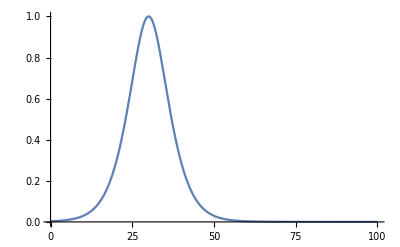

```mathematica
Plot[DpEps[h,30,4],{h,0,100},PlotRange->Full]
```

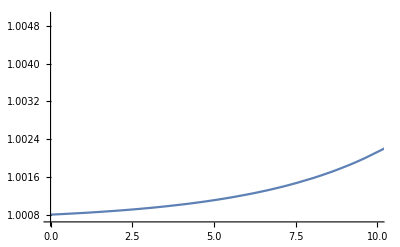

```mathematica
Plot[1+0.00065+0.05DpEps[h,30,4],{h,0,100},PlotRange->{{0,10},{1.00065,1.005}}]
```

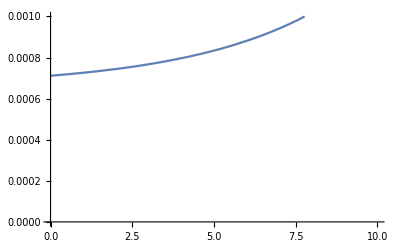

```mathematica
Plot[0.00065+0.02DpEps[h,30,4],{h,0,100},PlotRange->{{0,10},{0,0.001}}]
```

#### INDEX OF REFRACTION FITTING

##### LORENTZIAN

The atmospheric index of refraction will be fitted to a sum of Lorentzian functions:

```mathematica
Lorentzian[h_,h0_,a0_,b0_,c0_]:=Module[{},a0/(b0+c0(h-h0)^2)];
```

##### FITTING

Here, the fitting function is performed:

```mathematica
NonlinearModelFit[nedlen,Lorentzian[h,H1,A1,B1,C1]-Lorentzian[h,H2,A2,B2,C2],{A1,A2,B1,q0,q1,C1,B2,C2,H1,H2},h,MaxIterations->Infinity];
nfittedFull=%;
```

```mathematica
nfitted=nfittedFull//Normal
```

-222.666/(99.0621+0.157823 (7.1541+h)^2)+253.499/(112.757+0.179669 (7.15654+h)^2)

```mathematica
nfittedFull["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A1 | -222.666 | 0.000531179 | -419192. | 1.24402×10^-32
A2 | -253.499 | 0.000466666 | -543212. | 2.62717×10^-33
B1 | 99.0621 | 0.00123712 | 80075. | 2.56048×10^-28
q0 | 1. | 1.07894×10^-16 | 9.26839×10^15 | 1.06482×10^-94
q1 | 1. | 0. | ∞ | 0.
C1 | 0.157823 | 0.0315488 | 5.00251 | 0.00244622
B2 | 112.757 | 0.00100077 | 112670. | 3.29947×10^-29
C2 | 0.179669 | 0.0359186 | 5.00213 | 0.00244716
H1 | -7.1541 | 1.69093 | -4.23086 | 0.00549489
H2 | -7.15654 | 1.69164 | -4.23052 | 0.00549698

```mathematica
nfittedFull["BestFitParameters"]
```

{A1→-222.666,A2→-253.499,B1→99.0621,q0→1.,q1→1.,C1→0.157823,B2→112.757,C2→0.179669,H1→-7.1541,H2→-7.15654}

```mathematica
-7.1540968904797175
```

-7.1541

##### MODEL PLOTS

Here, we make plots of the fitted model:

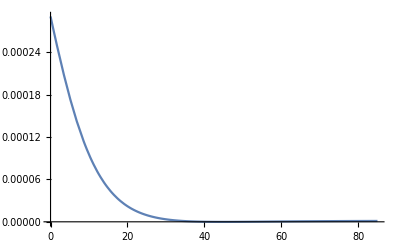

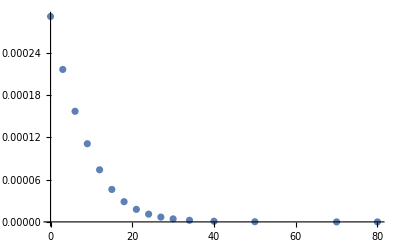

```mathematica
plt1=Plot[nfitted,{h,0,85},PlotRange->Full]
plt2=ListPlot[nedlen]
```

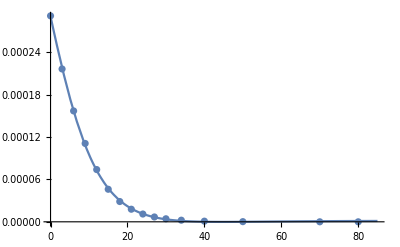

```mathematica
Show[plt1,plt2]
```

##### FORTRAN FORM MODEL

```mathematica
nfitted//FortranForm
```

-222.66559677864387/(99.06212001632495 + 0.15782316597789148*(7.1540968904797175 + h)**2) + 253.49880024119224/(112.75665221238798 + 0.17966910753975862*(7.156537366807337 + h)**2)

#### CLEAR VARIABLES

```mathematica
Clear[Psatm,Tsatm,nedlen]
Clear[Edlen,Lorentzian]
Clear[λ,Δns,nfitted,nfittedFull,plt1,plt2]
```

### IONOSPHERIC MODELS

#### APPLETON-HARTREE EQUATION

##### FULL EQUATION

Here is the Appleton-Hartree equation:

```mathematica
(* A USEFUL QUANTITY *)
Q=(1-X-ⅈ Z)^-1;

(* APPLETON-HARTREE EQUATION *)
nahsq=1-X/(1-ⅈ Z-(1/2 Y^2 Sin[θ]^2)Q+ε Q((1/2 Y^2 Sin[θ]^2)^2+(1-X)^2 Y^2 Cos[θ]^2)^(1/2));

Clear[Q];
```

##### DEFINITIONS

ANGLE θ

The angle θ is the angle formed between the direction of signal propagation and the ambient magnetic field (which is the Earth’s magnetic field in this case).

X

The quantity X:=(ω_p/ω)^2is defined in terms of the electron plasma frequency ω_p and ω=2π f, where f is the frequency of the signal.  The electron plasma frequency ω_p:=(n_e q^2)/(ϵ_0 m_e) is defined in terms of the electron number density n_e, q is the electron charge, m_e is the electron mass, and ϵ_0 is the vacuum permittivity.

```mathematica
repsωp={ωp->√(ne/(ϵ0 m))q};
repsX={X->1/(2 π freq)^2(ne q^2)/(ϵ0 m)};
```

Y

The quantity Y:=ω_H/ωis defined in terms of the electron gyro frequency ω_H:=(B_0 |q|)/m_e, where B_0 is the magnitude of the ambient magnetic field

```mathematica
repsωH={ωH->(B0 q)/m};
repsY={Y->ωH/(2 π freq)}/.repsωH;
```

Z

The quantity Z:=ν/ωis defined in terms of the electron collision frequency ν.

```mathematica
repsZ={Z->ν/(2 π freq)};
```

##### COLLISIONLESS PLASMA ASSUMPTION

```mathematica
nahsq/.{Z->0}//FullSimplify
```

1-(2 (-1+X) X)/(-2+2 X+Y^2 Sin[θ]^2-ε √(4 (-1+X)^2 Y^2 Cos[θ]^2+Y^4 Sin[θ]^4))

##### WEAK MAGNETIC FIELD ASSUMPTION

SETTING MAGNETIC FIELD TO ZERO

```mathematica
Series[nahsq^(1/2)/.{Z->0,Y->0},{X,0,1}]//Normal//FullSimplify
```

1-X/2

The Appleton-Hartree for (X≪1) is n_p=1-X/2. Since n_p<1, it must be a phase index of refraction.

EXPANDING IN Y

```mathematica
Series[nahsq^(1/2)/.{Z->0},{Y,0,1},{X,0,1}]//Normal;
FullSimplify[%,Assumptions->{Y>0,X<1}]
```

1+1/2 X (-1+Y ε √(Cos[θ]^2))

##### COMPUTE VALUES

RULES

Constants

```mathematica
repsconst={q->1.6*10^-19,m->9.1*10^-31,ϵ0->8.854*10^-12};
```

Signal frequency:

```mathematica
repsfreq={freq->10^9};
```

Earth’s magnetic field B_0 has a magnitude of 10^-4 T:

```mathematica
repsmag={B0->10^-4,q->1.6*10^-19,m->9.1*10^-31,ϵ0->8.854*10^-12,freq->10^9};
```

Earth’s magnetic field B_0 has a magnitude of 10^-4 T:

```mathematica
repsnemax={ne->10^6/((100^-1)^3)};
```

Concatenate rules

```mathematica
repsconc=Join[repsconst,repsfreq,repsmag,repsnemax];
```

COMPUTE MAGNITUDE FOR X & Y

```mathematica
(X/2)/.repsX/.repsconc
```

0.0000402411

```mathematica
Y/.repsY/.repsconc
```

0.00279833

```mathematica
Clear[repsconst,repsfreq,repsmag,repsnemax,nahsq]
```

##### TRUE INDEX OF REFRACTION

DISPERSION RELATION

To a first approximation, the dispersion relation for the ionosphere is ω^2=k^2+ω_p^2 where k is the wavenumber. Below are the replacement rules:

```mathematica
repsω={ω->√(k^2+ωp^2)};
repsωrev={ωp->√(ω^2-k^2)};
```

PHASE INDEX OF REFRACTION

The Appleton-Hartree equation yields the phase velocity, since it is less than unity. The phase velocity may be written in terms of k and ω_p in the following manner:

```mathematica
1/np==(ω/k/.repsω);
repsnp=Solve[%,np][[1]]
```

{np→k/(√(k^2+ωp^2))}

If k≪ω_p, one may expand in ω_p/k to obtain:

```mathematica
np/.repsnp;
Series[%,{ωp,0,2}]//Normal;
Simplify[%,Assumptions->k>0]
```

1-ωp^2/(2 k^2)

GROUP INDEX OF REFRACTION

The group velocity may be obtained by taking the derivative of the dispersion relation with respect to k:

```mathematica
ω/.repsω;
D[(%), k]//FullSimplify;
vg==%/.{vg->1/ng};
repsng=Solve[%,ng][[1]]
```

{ng→(√(k^2+ωp^2))/k}

Expand in ω_p/k to obtain:

```mathematica
ng/.repsng;
Series[%,{ωp,0,2}]//Normal;
Simplify[%,Assumptions->k>0]
```

1+ωp^2/(2 k^2)

It follows that given n_p=1-X/2 for the phase velocity (with X≪1), the group velocity is n_g=1+X/2.

#### LINE SHAPE FUNCTION

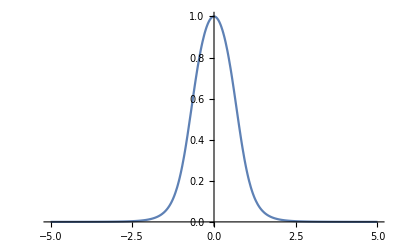

```mathematica
σ^2/(σ^2+(h-hc)^2)σ^4/(σ^4+(h-hc)^4);
Plot[%/.{hc->0,σ->1},{h,-5,5}]
```

#### EPSTEIN FUNCTION

##### DIMENSIONLESS EPSTEIN FUNCTION

```mathematica
DEps[h_,hc_,B_]:=Module[{},(4Exp[(h-hc)/B])/(1+Exp[(h-hc)/B])^2];
```

##### DIMENSIONLESS PSEUDO-EPSTEIN FUNCTION

```mathematica
DpEps[h_,hc_,B_]:=Module[{},
1/16(1/(1+((h-hc)/(2B))^2)+1/((1+((h-hc)/(4B))^2)^2)+1/((1+((h-hc)/(6B))^2)^3)+1/((1+((h-hc)/(7B))^2)^4))^2];
```

##### PLOTS

```mathematica
Plot[0DpEps[h,3,1]+DpEps[h,30,4],{h,0,100}, PlotRange->Full]
```

-Graphics-

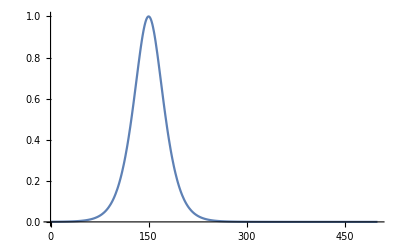

```mathematica
Plot[DpEps[h,150,15],{h,0,500}, PlotRange->Full]
```

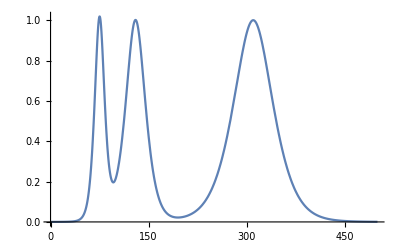

```mathematica
Plot[DpEps[h,75,5]+DpEps[h,130,10]+DpEps[h,310,20],{h,0,500}, PlotRange->Full]
```

##### COMPARISON

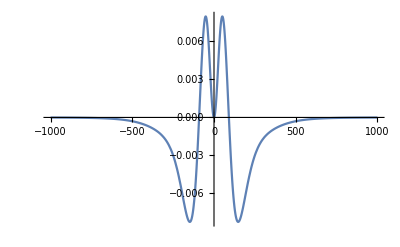

```mathematica
hc=0;
B=50;
Plot[DEps[h,hc,B]-DpEps[h,hc,B],{h,-1000,1000}, PlotRange->Full]
```

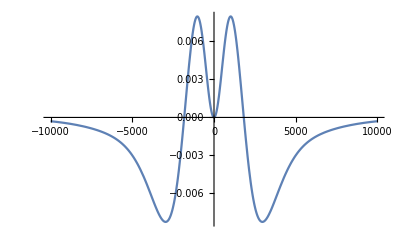

```mathematica
hc=0;
B=1000;
Plot[DEps[h,hc,B]-DpEps[h,hc,B],{h,-10000,10000}, PlotRange->Full]
```

#### IONOSPHERIC PROFILE

##### CONSTRUCTION

```mathematica
αD=(4.024105*^-17)*10^11
αE=(4.024105*^-17)*2.5*10^11
αF=(4.024105*^-17)*10^12
hD=75;
hE=130;
hF=300;
bD=5;
bE=30;
bF=50;
Δnio=αD*DpEps[h,hD,bD]+αE*DpEps[h,hE,bE]+αF*DpEps[h,hF,bF];
```

4.02411×10^-6

0.0000100603

0.0000402411

##### PLOT

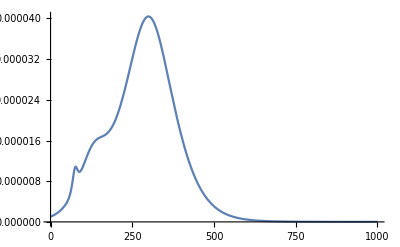

```mathematica
Plot[Δnio,{h,0,1000}]
```

```mathematica
0.00065*0.0003
```

1.95×10^-7

```mathematica
0.00004*0.01
```

4.×10^-7

##### FORTRAN FORM

```mathematica
Δnio;
%//FortranForm
```

2.515065625e-6*((1 + (-300 + h)**2/122500.)**(-4) + (1 + (-300 + h)**2/90000.)**(-3) + (1 + (-300 + h)**2/40000.)**(-2) + 1/(1 + (-300 + h)**2/10000.))**2 + 
     -  6.2876640625e-7*((1 + (-130 + h)**2/44100.)**(-4) + (1 + (-130 + h)**2/32400.)**(-3) + (1 + (-130 + h)**2/14400.)**(-2) + 1/(1 + (-130 + h)**2/3600.))**2 + 
     -  2.515065625e-7*((1 + (-75 + h)**2/1225.)**(-4) + (1 + (-75 + h)**2/900.)**(-3) + (1 + (-75 + h)**2/400.)**(-2) + 1/(1 + (-75 + h)**2/100.))**2

### CLEAR VARIABLES

```mathematica
Clear[Psatm,Tsatm,nedlen]
Clear[Edlen,Lorentzian]
Clear[λ,Δns,Δnio,nfitted,nfittedFull,plt1,plt2]
```

## SCURL

### NULL ENFORCER

Here, we compute the null condition.

#### CLEAR VARIABLES

```mathematica
Clear[g,V,V1,V2,V3,V4];
Clear[repsη1,repsη2,norm,repsV1A,repsV1B];
Clear[VV,f1,f2,f3,FV,JM];
```

#### METRIC AND FOUR-VELOCITY

```mathematica
g=({{g11, g12, g13, g14}, {g12, g22, g23, g24}, {g13, g23, g33, g34}, {g14, g24, g34, g44}});
V=({{V1}, {V2}, {V3}, {V4}});
```

```mathematica
repsη1={g11->-1,g11->1,g11->1,g11->1,g12->0,g13->0,g14->0,g23->0,g24->0,g34->0};
```

#### NULL CONDITION FOR FULL METRIC

```mathematica
Sum[V[[ai]]g[[ai,bi]]V[[bi]],{ai,1,4},{bi,1,4}];
norm=%//FullSimplify;
```

#### FULL METRIC

##### SOLVE NULL CONDITION

```mathematica
repsV1A=Solve[norm==0,V1]//FullSimplify
```

{{V1→-(g12 V2+g13 V3+g14 V4+1/2 √(4 (g12 V2+g13 V3+g14 V4)^2-4 g11 (g22 V2^2+2 g23 V2 V3+g33 V3^2+2 g24 V2 V4+2 g34 V3 V4+g44 V4^2)))/g11},{V1→(-2 g12 V2-2 g13 V3-2 g14 V4+√(4 (g12 V2+g13 V3+g14 V4)^2-4 g11 (g22 V2^2+2 g23 V2 V3+g33 V3^2+2 g24 V2 V4+2 g34 V3 V4+g44 V4^2)))/(2 g11)}}

##### COMPARE SOLUTIONS

```mathematica
(V1/.repsV1A[[1]])+(V1/.repsV1A[[2]])//FullSimplify
```

-(2 (g12 V2+g13 V3+g14 V4))/g11

```mathematica
%/.repsη1
```

0

##### FORTRAN FORM

```mathematica
V1/.repsV1A[[1]]//FortranForm
```

-((g12*V2 + g13*V3 + g14*V4 + Sqrt(4*(g12*V2 + g13*V3 + g14*V4)**2 - 4*g11*(g22*V2**2 + 2*g23*V2*V3 + g33*V3**2 + 2*g24*V2*V4 + 2*g34*V3*V4 + g44*V4**2))/2.)/g11)

```mathematica
V1/.repsV1A[[2]]//FortranForm
```

(-2*g12*V2 - 2*g13*V3 - 2*g14*V4 + Sqrt(4*(g12*V2 + g13*V3 + g14*V4)**2 - 4*g11*(g22*V2**2 + 2*g23*V2*V3 + g33*V3**2 + 2*g24*V2*V4 + 2*g34*V3*V4 + g44*V4**2)))/(2.*g11)

#### VANISHING g11 COMPONENT

##### SOLVE NULL CONDITION

```mathematica
repsV1B=Solve[(norm/.{g11->0})==0,V1][[1]]//FullSimplify
```

{V1→-(g22 V2^2+2 g23 V2 V3+g33 V3^2+2 g24 V2 V4+2 g34 V3 V4+g44 V4^2)/(2 (g12 V2+g13 V3+g14 V4))}

##### FORTRAN FORM

```mathematica
V1/.repsV1B//FortranForm
```

-0.5*(g22*V2**2 + 2*g23*V2*V3 + g33*V3**2 + 2*g24*V2*V4 + 2*g34*V3*V4 + g44*V4**2)/(g12*V2 + g13*V3 + g14*V4)

### ROOT FINDING PROBLEM

#### CLEAR VARIABLES

```mathematica
Clear[X1,X2,X3,X4];
Clear[V1,V2,V3,V4];
Clear[J1,J2,J3,J4];
Clear[VV,f1,f2,f3,FV,JM];
```

#### NULL GEODESIC INITIAL DATA

```mathematica
(* EMISSION POINTS (vi ABSTRACTLY REPRESENT 3-VELOCITIES) *)
X1={t1[v1],x1[v1],y1[v1],z1[v1]};
X2={t2[v2],x2[v2],y2[v2],z2[v2]};
X3={t3[v3],x3[v3],y3[v3],z3[v3]};
X4={t4[v4],x4[v4],y4[v4],z4[v4]};
```

```mathematica
(* INITIAL 3-VELOCITIES FOR NULL GEODESICS *)
V1={v1x,v1y,v1z};
V2={v2x,v2y,v2z};
V3={v3x,v3y,v3z};
V4={v4x,v4y,v4z};
```

```mathematica
(* CONCANTENATED INITIAL VELOCITIES - VARS TO BE SOLVED FOR *)
VV=Join[V1,V2,V3,V4];
```

#### EQUATIONS

```mathematica
(* EQUATIONS TO BE SOLVED ARE fi=0 *)
f1=X1-X2//Simplify;
f2=X1-X3//Simplify;
f3=X1-X4//Simplify;
```

```mathematica
(* EQUATIONS TO BE SOLVED ARE FV=0 *)
FV=Join[f1,f2,f3];
```

#### JACOBIAN STRUCTURE

Here, the derivatives of the function F(v) are used to construct the abstract Jacobian.

```mathematica
J1=D[FV, v1];
J2=D[FV, v2];
J3=D[FV, v3];
J4=D[FV, v4];
```

```mathematica
JM=List[J1,J2,J3,J4]//Transpose;
```

```mathematica
(* THE FOLLOWING DISPLAYS THE GENERAL STRUCTURE OF THE JACOBIAN *)
JM//MatrixForm
```

(t1'[v1] | -t2'[v2] | 0 | 0
x1'[v1] | -x2'[v2] | 0 | 0
y1'[v1] | -y2'[v2] | 0 | 0
z1'[v1] | -z2'[v2] | 0 | 0
t1'[v1] | 0 | -t3'[v3] | 0
x1'[v1] | 0 | -x3'[v3] | 0
y1'[v1] | 0 | -y3'[v3] | 0
z1'[v1] | 0 | -z3'[v3] | 0
t1'[v1] | 0 | 0 | -t4'[v4]
x1'[v1] | 0 | 0 | -x4'[v4]
y1'[v1] | 0 | 0 | -y4'[v4]
z1'[v1] | 0 | 0 | -z4'[v4])

The above may be converted into an 12×12 matrix by writing out the full derivatives of the final geodesic positions x^μ with respect to the 3-vectors v^i.